```mathematica
gh
```

```mathematica
Product[(1-z q^k)(1-q/z q^k),{k,0,Infinity}]
```

QPochhammer[q/z,q] QPochhammer[z,q]

```mathematica
Sum[(-p^-1)^k Q^(k(k-1)/2)-q^(1/2)x (-Qm p^-1)^k Q^(k(k-1)/2),{k,-2,2}]
```

1-1/p+Q/p^2-p Q+p^2 Q^3-√q x-(p^2 √q Q^3 x)/Qm^2+(p √q Q x)/Qm+(√q Qm x)/p-(√q Q Qm^2 x)/p^2

```mathematica
Series[Sum[(-p^-1)^k Q^(k(k-1)/2)-q^(1/2)x (-Qm p^-1)^k Q^(k(k-1)/2),{k,-2,2}],{Q,0,2}]
```

(-1+p-p √q x+√q Qm x)/p+(1/p^2-p+(p √q x)/Qm-(√q Qm^2 x)/p^2) Q+O[Q]^3

```mathematica
1/Series[QPochhammer[Q,Q],{Q,0,2}] Series[Sum[(-p^-1)^k Q^(k(k-1)/2)-q^(1/2)x (-Qm p^-1)^k Q^(k(k-1)/2),{k,-2,2}],{Q,0,2}]
```

(-1+p-p √q x+√q Qm x)/p+(1/p^2-p+(p √q x)/Qm-(√q Qm^2 x)/p^2+(-1+p-p √q x+√q Qm x)/p) Q+(1/p^2-p+(p √q x)/Qm-(√q Qm^2 x)/p^2+(2 (-1+p-p √q x+√q Qm x))/p) Q^2+O[Q]^3

```mathematica
Series[QPochhammer[Q,Q],{Q,0,2}]
```

1-Q-Q^2+O[Q]^3

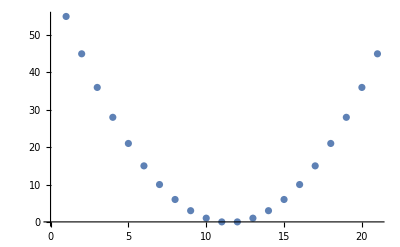

```mathematica
ListPlot[Table[k(k-1)/2,{k,-10,10}]]
```

```mathematica
Solve[n==k(k-1)/2,k,Integers]
```

{{k→ConditionalExpression[2 C[1],C[1]∈ℤ&&n+C[1]-2 C[1]^2==0]},{k→ConditionalExpression[1+2 C[1],C[1]∈ℤ&&n==C[1]+2 C[1]^2]}}

```mathematica
Series[Sum[(-z)^k Q^(k(k-1)/2),{k,-20,20}],{Q,0,30}]
```

(1-z)+(-1/z+z^2) Q+(1/z^2-z^3) Q^3+(-1/z^3+z^4) Q^6+(1/z^4-z^5) Q^10+(-1/z^5+z^6) Q^15+(1/z^6-z^7) Q^21+(-1/z^7+z^8) Q^28+O[Q]^31

```mathematica
Table[n^2/2+n/2,{n,0,7}]
```

{0,1,3,6,10,15,21,28}

```mathematica
Series[Sum[(-1)^k(z^(k)- z^(-k+1))Q^(k(k-1)/2),{k,0,7}],{Q,0,30}]-1+1z
```

(1-z)+(-1/z+z^2) Q+(1/z^2-z^3) Q^3+(-1/z^3+z^4) Q^6+(1/z^4-z^5) Q^10+(-1/z^5+z^6) Q^15+(1/z^6-z^7) Q^21+O[Q]^31

```mathematica
Series[Sum[(z)^k Q^(k(k-1)/2),{k,-20,20}],{Q,0,30}]
Series[Sum[(-1)^0(z^(k)+ z^(-k+1))Q^(k(k-1)/2),{k,0,7}],{Q,0,30}]-1-z
Series[Sum[(-1)^0(z^(k)+ z^(-k+1))Q^(k(k-1)/2),{k,1,7}],{Q,0,30}]
```

(1+z)+(1/z+z^2) Q+(1/z^2+z^3) Q^3+(1/z^3+z^4) Q^6+(1/z^4+z^5) Q^10+(1/z^5+z^6) Q^15+(1/z^6+z^7) Q^21+(1/z^7+z^8) Q^28+O[Q]^31

(1+z)+(1/z+z^2) Q+(1/z^2+z^3) Q^3+(1/z^3+z^4) Q^6+(1/z^4+z^5) Q^10+(1/z^5+z^6) Q^15+(1/z^6+z^7) Q^21+O[Q]^31

(1+z)+(1/z+z^2) Q+(1/z^2+z^3) Q^3+(1/z^3+z^4) Q^6+(1/z^4+z^5) Q^10+(1/z^5+z^6) Q^15+(1/z^6+z^7) Q^21+O[Q]^31

```mathematica
Series[Sum[1/(1+z)(z^(k)+ z^(-k+1))Q^(k(k-1)/2),{k,1,7}],{Q,0,30}]//Simplify
```

1+(-1+1/z+z) Q+((1/z^2+z^3) Q^3)/(1+z)+((1/z^3+z^4) Q^6)/(1+z)+((1/z^4+z^5) Q^10)/(1+z)+((1/z^5+z^6) Q^15)/(1+z)+((1/z^6+z^7) Q^21)/(1+z)+O[Q]^31

```mathematica
InverseSeries[Sum[Subscript[c, k] Q^(k(k-1)/2),{k,1,7}]+O[Q]^10]
```

(Q-c_1)/c_2-(c_3 (Q-c_1)^3)/c_2^4+(3 c_3^2 (Q-c_1)^5)/c_2^7-(c_4 (Q-c_1)^6)/c_2^7-(12 c_3^3 (Q-c_1)^7)/c_2^10+(9 c_3 c_4 (Q-c_1)^8)/c_2^10+(55 c_3^4 (Q-c_1)^9)/c_2^13+O[Q-c_1]^10

```mathematica
D[(z+m1 b + m2 b^-1)^-s,s]/.s->0
```

-Log[b m1+m2/b+z]

```mathematica
Exp[π I/2 x(x-b+b^-1)]/(Exp[π I/2 x(x-b+b^-1)]/.{x->x+b})//Simplify
```

-ⅈ ⅇ^(-ⅈ b π x)

```mathematica
(1-u)/(1-u^-1)//Simplify
```

-u

```mathematica
n=30;
qP[z_,q1_,q2_]:=Exp[Sum[-z^m/m*1/((1-q1^m)(1-q2^m)),{m,1,n}]];
qP[z_,q1_]:=Exp[Sum[-z^m/m*1/(1-q1^m),{m,1,n}]];
qTh[z_,q_]:=qP[z,q]qP[q/z,q];
qsTh[z_,q_]:=qP[q,q]^-1 Sum[(-1)^k z^k q^(k(k-1)/2),{k,-Floor[n/2],Floor[n/2]}];
```

```mathematica
(qP[u,q1,q2] (1-u)/(qP[u,q1]qP[u,q2]))/qP[u,q1^-1,q2^-1]//Cancel
```

-((ⅇ^(u/((1-1/q1) (1-1/q2))-u/((1-q1) (1-q2))+u^2/(2 (1-1/q1^2) (1-1/q2^2))-u^2/(2 (1-q1^2) (1-q2^2))+u^3/(3 (1-1/q1^3) (1-1/q2^3))-u^3/(3 (1-q1^3) (1-q2^3))+u^4/(4 (1-1/q1^4) (1-1/q2^4))-u^4/(4 (1-q1^4) (1-q2^4))+u^5/(5 (1-1/q1^5) (1-1/q2^5))-u^5/(5 (1-q1^5) (1-q2^5))+u^6/(6 (1-1/q1^6) (1-1/q2^6))-u^6/(6 (1-q1^6) (1-q2^6))+u^7/(7 (1-1/q1^7) (1-1/q2^7))-u^7/(7 (1-q1^7) (1-q2^7))+u^8/(8 (1-1/q1^8) (1-1/q2^8))-u^8/(8 (1-q1^8) (1-q2^8))+u^9/(9 (1-1/q1^9) (1-1/q2^9))-u^9/(9 (1-q1^9) (1-q2^9))+u^10/(10 (1-1/q1^10) (1-1/q2^10))-u^10/(10 (1-q1^10) (1-q2^10))) (-1+u))/((-1+q1 u) (-1+q1^2 u) (-1+q1^3 u) (-1+q1^4 u) (-1+q1^5 u) (-1+q1^6 u) (-1+q1^7 u) (-1+q1^8 u) (-1+q1^9 u) (-1+q1^10 u) (-1+q2 u) (-1+q2^2 u) (-1+q2^3 u) (-1+q2^4 u) (-1+q2^5 u) (-1+q2^6 u) (-1+q2^7 u) (-1+q2^8 u) (-1+q2^9 u) (-1+q2^10 u)))

```mathematica
Series[(qP[u q1,q1,q2]),{q1,0,3}]
```

1+(u q1)/(-1+q2)+((-u+q2^2 u+q2 u^2) q1^2)/((-1+q2)^2 (1+q2))+((u-q2^2 u-q2^3 u+q2^5 u-u^2-q2 u^2+q2^3 u^2+q2^4 u^2+q2^3 u^3) q1^3)/((-1+q2)^3 (1+q2) (1+q2+q2^2))+O[q1]^4

```mathematica
Series[1/(qP[u ,q1^-1,q2]),{q1,0,3}]
```

1+(u q1)/(-1+q2)+((-u+q2^2 u+q2 u^2) q1^2)/((-1+q2)^2 (1+q2))+((u-q2^2 u-q2^3 u+q2^5 u-u^2-q2 u^2+q2^3 u^2+q2^4 u^2+q2^3 u^3) q1^3)/((-1+q2)^3 (1+q2) (1+q2+q2^2))+O[q1]^4

```mathematica
Series[(qP[u,q1,q2]),{u,0,3}]
```

1-u/((-1+q1) (-1+q2))+((q1+q2) u^2)/((-1+q1)^2 (1+q1) (-1+q2)^2 (1+q2))+((-q1^3-q1 q2-q1^2 q2-q1 q2^2-q1^2 q2^2-q2^3) u^3)/((-1+q1)^3 (1+q1) (1+q1+q1^2) (-1+q2)^3 (1+q2) (1+q2+q2^2))+O[u]^4

```mathematica
Series[(qP[u,q1^-1,q2^-1]),{u,0,3}]
```

1-(q1 q2 u)/((-1+q1) (-1+q2))+((q1^3 q2^2+q1^2 q2^3) u^2)/((-1+q1)^2 (1+q1) (-1+q2)^2 (1+q2))-(q1^3 q2^3 (q1^3+q1 q2+q1^2 q2+q1 q2^2+q1^2 q2^2+q2^3) u^3)/((-1+q1)^3 (1+q1) (1+q1+q1^2) (-1+q2)^3 (1+q2) (1+q2+q2^2))+O[u]^4

```mathematica
Series[(1-u)/(qP[u,q1]qP[u,q2])*(qP[u,q1,q2]),{u,0,3}]
```

1-(q1 q2 u)/((-1+q1) (-1+q2))+((q1^3 q2^2+q1^2 q2^3) u^2)/((-1+q1)^2 (1+q1) (-1+q2)^2 (1+q2))+((-q1^6 q2^3-q1^4 q2^4-q1^5 q2^4-q1^4 q2^5-q1^5 q2^5-q1^3 q2^6) u^3)/((-1+q1)^3 (1+q1) (1+q1+q1^2) (-1+q2)^3 (1+q2) (1+q2+q2^2))+O[u]^4

```mathematica
Series[1/(qP[q1 u,q1]qP[u,q2])*(qP[u,q1,q2]),{u,0,3}]
```

1-(q1 q2 u)/((-1+q1) (-1+q2))+(q1^2 q2^2 (q1+q2) u^2)/((-1+q1)^2 (1+q1) (-1+q2)^2 (1+q2))+((-q1^6 q2^3-q1^4 q2^4-q1^5 q2^4-q1^4 q2^5-q1^5 q2^5-q1^3 q2^6) u^3)/((-1+q1)^3 (1+q1) (1+q1+q1^2) (-1+q2)^3 (1+q2) (1+q2+q2^2))+O[u]^4

```mathematica
Series[(qP[u^-1,q1^-1,q2^-1]),{q1,0,3}]
```

1+(q2 q1)/((-1+q2) u)+((q2^3-q2 u+q2^3 u) q1^2)/((-1+q2)^2 (1+q2) u^2)+(q2 (q2^5-q2 u-q2^2 u+q2^4 u+q2^5 u+u^2-q2^2 u^2-q2^3 u^2+q2^5 u^2) q1^3)/((-1+q2)^3 (1+q2) (1+q2+q2^2) u^3)+O[q1]^4

```mathematica
Series[(qP[u^-1 q1 q2,q1,q2]),{q1,0,3}]
```

1+(q2 q1)/((-1+q2) u)+((q2^3-q2 u+q2^3 u) q1^2)/((-1+q2)^2 (1+q2) u^2)+((q2^6-q2^2 u-q2^3 u+q2^5 u+q2^6 u+q2 u^2-q2^3 u^2-q2^4 u^2+q2^6 u^2) q1^3)/((-1+q2)^3 (1+q2) (1+q2+q2^2) u^3)+O[q1]^4

```mathematica
Series[(1/qP[u^-1  q2,q2]*qP[u^-1,q1,q2]/qP[u^-1 ,q1]),{q1,0,3}]
```

1+(q2 q1)/((-1+q2) u)+((q2^3-q2 u+q2^3 u) q1^2)/((-1+q2)^2 (1+q2) u^2)+((q2^6-q2^2 u-q2^3 u+q2^5 u+q2^6 u+q2 u^2-q2^3 u^2-q2^4 u^2+q2^6 u^2) q1^3)/((-1+q2)^3 (1+q2) (1+q2+q2^2) u^3)+O[q1]^4

```mathematica
Series[((1-u^-1)/qP[u^-1 ,q2]*qP[u^-1,q1,q2]/qP[u^-1 ,q1]),{q2,0,3}]
```

ⅇ^((252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) (1-1/u)+(ⅇ^((252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) q1 (1-1/u) q2)/((-1+q1) u)+(ⅇ^(1/(10 u^10)+1/(9 u^9)+1/(8 u^8)+1/(7 u^7)+1/(6 u^6)+1/(5 u^5)+1/(4 u^4)+1/(3 u^3)+1/(2 u^2)+1/u) q1 (-1+u) (q1^2-u+q1^2 u) q2^2)/((-1+q1)^2 (1+q1) u^3)+(ⅇ^(1/(10 u^10)+1/(9 u^9)+1/(8 u^8)+1/(7 u^7)+1/(6 u^6)+1/(5 u^5)+1/(4 u^4)+1/(3 u^3)+1/(2 u^2)+1/u) q1 (-1+u) (q1^5-q1 u-q1^2 u+q1^4 u+q1^5 u+u^2-q1^2 u^2-q1^3 u^2+q1^5 u^2) q2^3)/((-1+q1)^3 (1+q1) (1+q1+q1^2) u^4)+O[q2]^4

```mathematica
Series[qP[u^-1,q2]/(1-u^-1),{q2,0,3}]//Simplify
```

(ⅇ^(-(252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) u)/(-1+u)-(ⅇ^(-(252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) q2)/(-1+u)-(ⅇ^(-(252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) q2^2)/(-1+u)-(ⅇ^(-(252+280 u+315 u^2+360 u^3+420 u^4+504 u^5+630 u^6+840 u^7+1260 u^8+2520 u^9)/(2520 u^10)) q2^3)/u+O[q2]^4

```mathematica
Out[155]-Out[164]
```

O[u]^4

```mathematica
Series[1/(qP[u ,q1^-1]),{q1,0,3}]
```

O[q1]^55

```mathematica
Series[1/(qTh[z,q^2]qTh[ z,q^-1]),{q,0,3}]//Simplify
```

ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10)-(ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10) (1+z^2) q)/z+ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10) q^2-(ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10) (1+z^2) q^3)/z+O[q]^4

```mathematica
Series[qsTh[q^-2 z,q^-2]qsTh[ q^1 z,q^1],{q,0,3}]//Simplify
```

$Aborted

```mathematica
Series[qTh[q z,q^2],{q,0,3}]
```

1+(-1/z-z) q+q^2+((-1-z^2) q^3)/z+O[q]^4

```mathematica
Series[qTh[ z,q^1]/qTh[ z,q^2],{q,0,3}]//Simplify
```

1-((1+z^2) q)/z+q^2-((1+z^2) q^3)/z+O[q]^4

```mathematica
Out[277]-Out[276]
```

O[q]^4

```mathematica
Series[qP[u,q]/qP[u,q^2],{q,0,3}]//Simplify
```

1-u q-u q^3+O[q]^4

```mathematica
Series[qP[q u,q^2],{q,0,3}]//Simplify
```

1-u q-u q^3+O[q]^4

```mathematica
Table[Series[qTh[q z q^k,q^2]/qTh[q z q^0,q^2],{q,0,3}],{k,-2,2}]
```

{ⅇ^(-z^10/(10 q^10)-z^9/(9 q^9)-z^8/(8 q^8)-z^7/(7 q^7)-z^6/(6 q^6)-z^5/(5 q^5)-z^4/(4 q^4)-z^3/(3 q^3)-z^2/(2 q^2)-z/q+q/z+q^2/(2 z^2)+q^3/(3 z^3)+O[q]^4),ⅇ^((-2520 z-1260 z^2-840 z^3-630 z^4-504 z^5-420 z^6-360 z^7-315 z^8-280 z^9-252 z^10)/2520)+ⅇ^((-2520 z-1260 z^2-840 z^3-630 z^4-504 z^5-420 z^6-360 z^7-315 z^8-280 z^9-252 z^10)/2520) (1/z+z) q+1/2 ⅇ^((-2520 z-1260 z^2-840 z^3-630 z^4-504 z^5-420 z^6-360 z^7-315 z^8-280 z^9-252 z^10)/2520) ((1/z+z)^2+(1-2 z-2 z^3+z^4)/z^2) q^2+(ⅇ^(-z-z^2/2-z^3/3-z^4/4-z^5/5-z^6/6-z^7/7-z^8/8-z^9/9-z^10/10) (1-z+2 z^2-2 z^3+2 z^4-z^5+z^6) q^3)/z^3+O[q]^4,1,ⅇ^((-252-280 z-315 z^2-360 z^3-420 z^4-504 z^5-630 z^6-840 z^7-1260 z^8-2520 z^9)/(2520 z^10))+ⅇ^((-252-280 z-315 z^2-360 z^3-420 z^4-504 z^5-630 z^6-840 z^7-1260 z^8-2520 z^9)/(2520 z^10)) (1/z+z) q+1/2 ⅇ^((-252-280 z-315 z^2-360 z^3-420 z^4-504 z^5-630 z^6-840 z^7-1260 z^8-2520 z^9)/(2520 z^10)) ((1/z+z)^2+(1-2 z-2 z^3+z^4)/z^2) q^2+(ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z) (1-z+2 z^2-2 z^3+2 z^4-z^5+z^6) q^3)/z^3+O[q]^4,ⅇ^(-1/(10 z^10 q^10)-1/(9 z^9 q^9)-1/(8 z^8 q^8)-1/(7 z^7 q^7)-1/(6 z^6 q^6)-1/(5 z^5 q^5)-1/(4 z^4 q^4)-1/(3 z^3 q^3)-1/(2 z^2 q^2)-1/(z q)+z q+(z^2 q^2)/2+(z^3 q^3)/3+O[q]^4)}

```mathematica
Series[1/(qTh[z ,q]qTh[z ,q^-1]),{q,0,4}]//Simplify
```

ⅇ^(-1/(20 z^20)-1/(19 z^19)-1/(18 z^18)-1/(17 z^17)-1/(16 z^16)-1/(15 z^15)-1/(14 z^14)-1/(13 z^13)-1/(12 z^12)-1/(11 z^11)-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10+z^11/11+z^12/12+z^13/13+z^14/14+z^15/15+z^16/16+z^17/17+z^18/18+z^19/19+z^20/20)+O[q]^5

```mathematica
FullSimplify[
Exp[
Sum[(z q)^k/k,{k,1,Infinity}]-Sum[(z q)^(-k)/k,{k,1,Infinity}]   
],
{q>0,z>0}]
```

-1/(q z)

```mathematica
Series[qsTh[q z ,q^2],{q,0,10}]//Simplify
```

1-((1+z^2) q)/z+q^2-((1+z^2) q^3)/z+(2+1/z^2+z^2) q^4-(2 (1+z^2) q^5)/z+(3+1/z^2+z^2) q^6-(3 (1+z^2) q^7)/z+(5+2 (1/z^2+z^2)) q^8-((1+5 z^2+5 z^4+z^6) q^9)/z^3+(7+3 (1/z^2+z^2)) q^10+O[q]^11

```mathematica
Series[qsTh[ q z^(+1) ,q^4]qsTh[ q z^-1 ,q^4],{q,0,10}]//Simplify
```

1-((1+z^2) q)/z+q^2-((1+z^2) q^3)/z+(2+1/z^2+z^2) q^4-(2 (1+z^2) q^5)/z+(3+1/z^2+z^2) q^6-(3 (1+z^2) q^7)/z+(5+2/z^2+2 z^2) q^8-((1+5 z^2+5 z^4+z^6) q^9)/z^3+(7+3/z^2+3 z^2) q^10+O[q]^11

```mathematica
Series[(qsTh[ q z^(+1) ,q^4]qsTh[ q z^-1 ,q^4])/qsTh[q z ,q^2],{q,0,20}]//Simplify
```

1+O[q]^21

```mathematica
Series[qsTh[ q z^1 q^1 ,q^4]/qsTh[ q z^1 ,q^4],{q,0,2}]//Simplify
```

1+z q+(-1/z-z+z^2) q^2+O[q]^3

```mathematica
(Series[qsTh[ q z^1 q^2 ,q^4]/qsTh[ q z^1 ,q^4] qsTh[ q z^-1 q^-2 ,q^4]/qsTh[ q z^-1 ,q^4],{q,0,3}]//Simplify)
```

-1/(z q)+O[q]^4

```mathematica
(Series[qsTh[ q z^1 q^4 ,q^4]/qsTh[ q z^1 ,q^4] qsTh[ q z^-1 q^-4 ,q^4]/qsTh[ q z^-1 ,q^4],{q,0,3}]//Simplify)
```

1/(z^2 q^4)+O[q]^4

```mathematica
(Series[qsTh[ q z^1 q^6 ,q^4]/qsTh[ q z^1 ,q^4] qsTh[ q z^-1 q^-6 ,q^4]/qsTh[ q z^-1 ,q^4],{q,0,3}]//Simplify)
```

-1/(z^3 q^9)+O[q]^4

```mathematica
(Series[qsTh[ q z^1 q^1 ,q^4]/qsTh[ q z^1 ,q^4],{q,0,3}]//Simplify)
```

1+z q+(-1/z-z+z^2) q^2+(-1+1/z-z^2+z^3) q^3+O[q]^4

```mathematica
Series[qP[q,q]qsTh[z ,q],{q,0,4}]
```

(1-z)+(-1/z+z^2) q+(1/z^2-z^3) q^3+O[q]^5

```mathematica
Series[qsTh[z ,q],{q,0,4}]
```

(1-z)+(1-1/z-z+z^2) q+(2 (1-z)-1/z+z^2) q^2+(3 (1-z)+1/z^2-z^3+2 (-1/z+z^2)) q^3+(5 (1-z)+1/z^2-z^3+3 (-1/z+z^2)) q^4+O[q]^5

```mathematica
Series[qP[q^2,q^2]qsTh[- z^2 q ,q^2],{q,0,4}]
```

1+(1/z^2+z^2) q+(1/z^4+z^4) q^4+O[q]^5

```mathematica
Series[EllipticTheta[3,I Log[z],q],{q,0,4}]//TrigToExp
```

1+(1/z^2+z^2) q+(1/z^4+z^4) q^4+O[q]^5

```mathematica
qTh[q z  ,q ]/(qTh[z , q])/.{q->0.1,z->0.9}//N
```

0.00407563

```mathematica
z
```

```mathematica
Solve[{a ==n1-n2,b ==n1+n2},{n1,n2}]
```

{{n1→(a+b)/2,n2→1/2 (-a+b)}}

```mathematica
Series[-z/(qTh[z,q]qTh[z,q^-1]),{q,0,4}]//Simplify
```

-ⅇ^(-1/(10 z^10)-1/(9 z^9)-1/(8 z^8)-1/(7 z^7)-1/(6 z^6)-1/(5 z^5)-1/(4 z^4)-1/(3 z^3)-1/(2 z^2)-1/z+z+z^2/2+z^3/3+z^4/4+z^5/5+z^6/6+z^7/7+z^8/8+z^9/9+z^10/10) z+O[q]^5

```mathematica
-h/4(a-b)^2+h/4(a+b)^2//Simplify
```

a b h

```mathematica
FullSimplify[q^(h v^2/4),{u>0,q>0,m>0, m ϵ Integers}]
```

q^((h v^2)/4)

```mathematica
q^((1+m)^2+Log[u]^2/(4 Log[q]^2)) u^(1+m)/.m->0
```

q^(1+Log[u]^2/(4 Log[q]^2)) u

```mathematica
(Log[u ]+Log[q^(2m + 2)])^2//Expand
```

Log[q^(2+2 m)]^2+2 Log[q^(2+2 m)] Log[u]+Log[u]^2

```mathematica
((q1 q2)^(-h/2))^(-1* (Log[u1]^2+Log[u2]^2)/(2 Log[q1]Log[q2]))
```

((q1 q2)^(-h/2))^(-(Log[u1]^2+Log[u2]^2)/(2 Log[q1] Log[q2]))

```mathematica
FullSimplify[(((q1 q2)^(-h/2))^(-1* (Log[u1]^2+Log[u2]^2)/(2 Log[q1]Log[q2]))/.{q1->q1^-1,q2->q2^-1})/(((q1 q2)^(-h/2))^(-1* (Log[u1]^2+Log[u2]^2)/(2 Log[q1]Log[q2]))),{Element[{q1,q2,u1,u2,h},Reals],q1>0,q2>0}]
```

(q1 q2)^(-(h (Log[u1]^2+Log[u2]^2))/(2 Log[q1] Log[q2]))

```mathematica
FullSimplify[(q1 q2)^(-(h (Log[u1]^2+Log[u2]^2))/(2 Log[q1] Log[q2]))/.{u1->u^(-1/2),u2->u^(1/2),q1->q^{-1},q2->q^2,h->2},{Element[{q1,q2,q,u1,u2,u,h},Reals],q>0,h>0,u>0,u2>0}]
```

{ⅇ^(Log[u]^2/Log[q^4])}

```mathematica
Solve[{u==u1/u2,u1 u2 ==1},{u1,u2}]
```

{{u1→-√u,u2→-1/(√u)},{u1→√u,u2→1/(√u)}}

```mathematica
FullSimplify[-(h ((Log[u1])^2+Log[u2]^2))/(2 Log[q1] Log[q2])/.{u1->u^(-1/2),u2->u^(1/2),q1->q^{-1},q2->q^2,h->2},{Element[{q1,q2,q,u1,u2,u,h},Reals],q>0,h>0,u>0,u2>0}]
```

{Log[u]^2/(4 Log[q]^2)}

```mathematica
(Log[u]+Log[u2])
```

```mathematica
FullSimplify[ Log[1/q1] ,{Element[{q1,q2,u1,u2,h},Reals],q1>0}]
```

-Log[q1]

```mathematica
Series[ArcSin[x],{x,0,10}]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^11

```mathematica
Series[EllipticTheta[z,Q,3],{Q,0,10}]
```

EllipticTheta[z,0,3]+EllipticThetaPrime[z,0,3] Q+1/2 EllipticThetaPrime^(0,1,0)[z,0,3] Q^2+1/6 EllipticThetaPrime^(0,2,0)[z,0,3] Q^3+1/24 EllipticThetaPrime^(0,3,0)[z,0,3] Q^4+1/120 EllipticThetaPrime^(0,4,0)[z,0,3] Q^5+1/720 EllipticThetaPrime^(0,5,0)[z,0,3] Q^6+(EllipticThetaPrime^(0,6,0)[z,0,3] Q^7)/5040+(EllipticThetaPrime^(0,7,0)[z,0,3] Q^8)/40320+(EllipticThetaPrime^(0,8,0)[z,0,3] Q^9)/362880+(EllipticThetaPrime^(0,9,0)[z,0,3] Q^10)/3628800+O[Q]^11

```mathematica
Sum[(-z)^k Q^(k(k-1)/2),{k,-Infinity,Infinity}]
```

∑_(k=-∞)^∞ Q^(1/2 (-1+k) k) (-z)^k

```mathematica
D2Roots = Flatten[Table[If[EvenQ[a+b],{a,b},Nothing],{a,-1,1},{b,-1,1}],1];
sum1 = Flatten[Table[n1+n2,{n1,D2Roots},{n2,D2Roots}],1];
sum2= Flatten[Table[n1-n2,{n1,D2Roots},{n2,D2Roots}],1];
sumplus = Flatten[Table[1nplus,{nplus,D2Roots}],0];
```

```mathematica
D4RootLattice=  Table[If[a.a≤4,a,Nothing],{a,Flatten[Table[If[EvenQ[a+b+c+d],{a,b,c,d},Nothing],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2}],3]}];
D4Roots = Table[If[a.a==2,a,Nothing],{a,D4RootLattice}];
B4Roots = Join[D4Roots,Flatten[Table[If[a^2+b^2+c^2+d^2==1,{a,b,c,d},Nothing],{a,-1,1},{b,-1,1},{c,-1,1},{d,-1,1}],3]];
D4λclass ={{0,0,0,0},{1,0,0,0},{1/2,1/2,1/2,-1/2},{1/2,1/2,1/2,1/2}} ;
D40class = Table[If[a.a≤ 3,a,Nothing],{a,D4RootLattice}];
D41class =Table[If[(a+{1,0,0,0}).(a+{1,0,0,0})≤ 3,a+{1,0,0,0},Nothing],{a,D4RootLattice}];
D43class = Table[a+{1/2,1/2,1/2,-1/2},{a,D40class}];
D44class = Table[a+{1/2,1/2,1/2,1/2},{a,D40class}];
D4WeightLattice = Join[Flatten[Table[Table[a+L,{a,D4RootLattice}],{L,D4λclass}],1]];
D4SmallWeights = Table[If[a.a<=1,a,Nothing],{a,D4WeightLattice}]
D4Fundamental = {{0,0,0,0},{1,0,0,0},{1,1,0,0},{1/2,1/2,1/2,-1/2},{1/2,1/2,1/2,1/2}} ;
D2RootLattice= Table[If[a.a≤8,a,Nothing],{a,Flatten[Table[If[EvenQ[a+b],{a,b},Nothing],{a,-4,4},{b,-4,4}],1]}];
D2Roots = Table[If[a.a==2,a,Nothing],{a,D2RootLattice}];
B2Roots = Join[D2Roots,{{1,0},{-1,0},{0,1},{0,-1}}];
D3Roots = Flatten[Table[If[EvenQ[a+b+c]&&{a,b,c}.{a,b,c}==2,{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2];
B3Roots = Join[D3Roots,Flatten[Table[If[a^2+b^2+c^2==1,{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]];
D2λclass ={{0,0},{1,0},{1/2,1/2},{1/2,-1/2}} ;
D20class = D2RootLattice;
D21class = Table[a+{1,0},{a,D2RootLattice}];
D23class = Table[a+{1/2,1/2},{a,D2RootLattice}];
D24class = Table[a+{1/2,-1/2},{a,D2RootLattice}];
D2WeightLattice = Join[Flatten[Table[Table[a+L,{a,D2RootLattice}],{L,D2λclass}],1]];
D2SmallWeights = Table[If[a.a<=1,a,Nothing],{a,D2WeightLattice}];
D2Fundamental = {{0,0},{1,0},{1,1},{1/2,-1/2},{1/2,1/2}} ;
A1RootLattice= Table[If[a.a≤8,a,Nothing],{a,Flatten[Table[If[a+b==0,{a,b},Nothing],{a,-4,4},{b,-4,4}],1]}];
A1Roots = Table[If[a.a==2,a,Nothing],{a,A1RootLattice}];
A10class = Join[A1Roots,{{0,0}}];
A11class = Table[a+{1,0},{a,A1RootLattice}];
A12class = Table[a-{1,0},{a,A1RootLattice}];
```

{{0,0,0,0},{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1},{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0},{-1/2,-1/2,-1/2,1/2},{-1/2,-1/2,1/2,-1/2},{-1/2,1/2,-1/2,-1/2},{-1/2,1/2,1/2,1/2},{1/2,-1/2,-1/2,-1/2},{1/2,-1/2,1/2,1/2},{1/2,1/2,-1/2,1/2},{1/2,1/2,1/2,-1/2},{-1/2,-1/2,-1/2,-1/2},{-1/2,-1/2,1/2,1/2},{-1/2,1/2,-1/2,1/2},{-1/2,1/2,1/2,-1/2},{1/2,-1/2,-1/2,1/2},{1/2,-1/2,1/2,-1/2},{1/2,1/2,-1/2,-1/2},{1/2,1/2,1/2,1/2}}

```mathematica
Table[Sum[If[a.L==1,a,0],{a,D4Roots}]-6L,{L,D4Fundamental}]
```

{{0,0,0,0},{0,0,0,0},{-2,-2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Table[Sum[k Sum[If[a.L==k,a,0],{a,D4Roots}],{k,1,10}]-6L,{L,D4WeightLattice}]//Tally
```

{{{0,0,0,0},1252}}

```mathematica
6{1,1,0,0}
Product[If[a.{1,1,0,0}==1,(-q),1],{a,D4Roots}]Product[If[a.{1,1,0,0}==2,q^4,1],{a,D4Roots}]
q^(6{1,1,0,0}.{1,1,0,0})
```

{{{-10,-10,-10,-10},1},{{-10,-10,-10,0},1},{{-10,-10,-10,10},1},{{-10,-10,-5,-5},1},{{-10,-10,-5,5},1},{{-10,-10,0,-10},1},{{-10,-10,0,0},1},1238,{{25/2,25/2,5/2,5/2},1},{{25/2,25/2,5/2,25/2},1},{{25/2,25/2,15/2,-5/2},1},{{25/2,25/2,15/2,15/2},1},{{25/2,25/2,25/2,-15/2},1},{{25/2,25/2,25/2,5/2},1},{{25/2,25/2,25/2,25/2},1}}
 |  |  |  |

```mathematica
(Subscript[τp, 3/2] Subscript[τm, 1/2]+Subscript[τp, 1/2] Subscript[τm, 3/2])(Subscript[τp, -3/2] Subscript[τm, -1/2]+Subscript[τp, -1/2] Subscript[τm, -3/2])-(Subscript[τp, 1/2] Subscript[τm, -1/2]+Subscript[τp, -1/2] Subscript[τm, 1/2])(Subscript[τp, 3/2] Subscript[τm, -3/2]+Subscript[τp, -3/2] Subscript[τm, 3/2])
```

-(τm_(1/2) τp_(-1/2)+τm_(-1/2) τp_(1/2)) (τm_(3/2) τp_(-3/2)+τm_(-3/2) τp_(3/2))+(τm_(-1/2) τp_(-3/2)+τm_(-3/2) τp_(-1/2)) (τm_(3/2) τp_(1/2)+τm_(1/2) τp_(3/2))

```mathematica
Simplify[(Subscript[τp, 5/2] Subscript[τm, 3/2]+Subscript[τp, 3/2] Subscript[τm, 5/2])(Subscript[τp, -5/2] Subscript[τm, -3/2]+Subscript[τp, -3/2] Subscript[τm, -5/2])-(Subscript[τp, 3/2] Subscript[τm, -3/2]+Subscript[τp, -3/2] Subscript[τm, 3/2])(Subscript[τp, 5/2] Subscript[τm, -5/2]+Subscript[τp, -5/2] Subscript[τm, 5/2])/.{h->1}]
```

-(τm_(3/2) τp_(-5/2)-τm_(-5/2) τp_(3/2)) (τm_(5/2) τp_(-3/2)-τm_(-3/2) τp_(5/2))

```mathematica
Simplify[Subscript[τp, 1] Subscript[τm, 1] Subscript[τp, -1] Subscript[τm, -1]-1/4(Subscript[τp, 1] Subscript[τm, -1]+Subscript[τp, -1] Subscript[τm, 1])^2]
```

-1/4 (τm_1 τp_-1-τm_-1 τp_1)^2

```mathematica
τ0D2[u1_,u2_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] z^(1/2m.m+i+m.{Log[u1],Log[u2]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]]]],{m,D20class},{i,0,3}];
τ1D2[u1_,u2_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] z^(1/2m.m+i+m.{Log[u1],Log[u2]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]]]],{m,D21class},{i,0,3}];
τ0D4[u1_,u2_,u3_,u4_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] ξ3^m[[3]] ξ4^m[[4]] z^(1/2m.m+i+m.{Log[u1],Log[u2],Log[u3],Log[u4]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]],u3 q^m[[3]],u4 q^m[[4]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]],u3 q^m[[3]],u4 q^m[[4]]]],{m,D40class},{i,0,3}];
τ1D4[u1_,u2_,u3_,u4_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] ξ3^m[[3]] ξ4^m[[4]] z^(1/2m.m+i+m.{Log[u1],Log[u2],Log[u3],Log[u4]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]],u3 q^m[[3]],u4 q^m[[4]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]],u3 q^m[[3]],u4 q^m[[4]]]],{m,D41class},{i,0,3}];
τ0A1[u1_,u2_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] z^(1/2m.m+i+m.{Log[u1],Log[u2]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]]]],{m,A10class},{i,0,1}];
τ1A1[u1_,u2_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] z^(1/2m.m+i+m.{Log[u1],Log[u2]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]]]],{m,A11class},{i,0,1}];
τ2A1[u1_,u2_,z_] := Sum[ϵ^(1/2m.m+i)ξ1^m[[1]] ξ2^m[[2]] z^(1/2m.m+i+m.{Log[u1],Log[u2]}/Log[q])Subscript[B, 0][u1 q^m[[1]],u2 q^m[[2]]]If[i==0,1,Subscript[Z, i][u1 q^m[[1]],u2 q^m[[2]]]],{m,A12class},{i,0,1}];
```

```mathematica
Take[Range[10],-5]
```

{6,7,8,9,10}

```mathematica
Table[Simplify[Coefficient[Coefficient[Coefficient[τ0D2[u1,u2,q z]τ0D2[u1,u2,q^-1 z]-τ0D2[u1,u2,z]^2,ξ1,k],ξ2,l],ϵ,m]==Coefficient[Coefficient[Coefficient[τ1D2[u1,u2,q z]τ1D2[u1,u2,q^-1 z]-τ1D2[u1,u2,z]^2,ξ1,k],ξ2,l],ϵ,m],{u1>0,u2>0,q>0,z>0}],{k,-1,1},{l,-1,1},{m,1,1}]
```

{{{((1/(u1 u2))^(1+Log[z]/Log[q]) (q-u1 u2)^2 z B_0[u1,u2] B_0[u1/q,u2/q])/q==z^(-(3 Log[u1 u2])/Log[q]) (-2 z^(1+(2 Log[u1 u2])/Log[q])+(u1/u2+u2/u1) z^(Log[q u1^2 u2^2]/Log[q])) B_0[u1,u2/q] B_0[u1/q,u2]},{True},{(u1-q u2)^2 B_0[u1,u2] B_0[u1/q,q u2]==q (-1+u1 u2)^2 B_0[u1,q u2] B_0[u1/q,u2]}},{{True},{u2^2 (-q (-1+u1^2)^2 B_0[u1/q,u2] B_0[q u1,u2]+(-1+q)^2 u1^2 B_0[u1,u2]^2 Z_1[u1,u2])==q u1^2 (-1+u2^2)^2 B_0[u1,u2/q] B_0[u1,q u2]},{True}},{{(-q u1+u2)^2 B_0[u1,u2] B_0[q u1,u2/q]==q (-1+u1 u2)^2 B_0[u1,u2/q] B_0[q u1,u2]},{True},{q (u1-u2)^2 z^(Log[q u1 u2]/Log[q]) B_0[u1,q u2] B_0[q u1,u2]==(u1 u2)^(Log[z]/Log[q]) (-1+q u1 u2)^2 z B_0[u1,u2] B_0[q u1,q u2]}}}

```mathematica
Table[Simplify[Coefficient[Coefficient[Coefficient[τ0D2[u1,u2,q z]τ0D2[u1,u2,q^-1 z]-τ0D2[u1,u2,z]^2,ξ1,0],ξ2,0],ϵ,m]==Coefficient[Coefficient[Coefficient[τ1D2[u1,u2,q z]τ1D2[u1,u2,q^-1 z]-τ1D2[u1,u2,z]^2,ξ1,0],ξ2,0],ϵ,m],{u1>0,u2>0,q>0,z>0}],{m,1,3}]
```

{u2^2 (-q (-1+u1^2)^2 B_0[u1/q,u2] B_0[q u1,u2]+(-1+q)^2 u1^2 B_0[u1,u2]^2 Z_1[u1,u2])==q u1^2 (-1+u2^2)^2 B_0[u1,u2/q] B_0[u1,q u2],1/(q^2 u1^2 u2^2)z^2 (q^2 (u1^2-u2^2)^2 B_0[u1/q,q u2] B_0[q u1,u2/q]+q^2 (-1+u1^2 u2^2)^2 B_0[u1/q,u2/q] B_0[q u1,q u2]-q (u1 u2)^((2 Log[z])/Log[q]) z^(-(2 Log[u1 u2])/Log[q]) (u1^2 B_0[u1,u2/q] B_0[u1,q u2] ((q-u2^2)^2 Z_1[u1,u2/q]+(-1+q u2^2)^2 Z_1[u1,q u2])+u2^2 B_0[u1/q,u2] B_0[q u1,u2] ((q-u1^2)^2 Z_1[u1/q,u2]+(-1+q u1^2)^2 Z_1[q u1,u2]))+(-1+q^2)^2 u1^2 u2^2 B_0[u1,u2]^2 Z_2[u1,u2])==0,1/(q^3 u1^2 u2^2)z^3 (q^2 B_0[u1/q,q u2] B_0[q u1,u2/q] ((u1^2-q u2^2)^2 Z_1[u1/q,q u2]+(-q u1^2+u2^2)^2 Z_1[q u1,u2/q])+q^2 B_0[u1/q,u2/q] B_0[q u1,q u2] ((q-u1^2 u2^2)^2 Z_1[u1/q,u2/q]+(-1+q u1^2 u2^2)^2 Z_1[q u1,q u2])-q (u1 u2)^((2 Log[z])/Log[q]) z^(-(2 Log[u1 u2])/Log[q]) (u1^2 B_0[u1,u2/q] B_0[u1,q u2] (q^2 (-1+u2^2)^2 Z_1[u1,u2/q] Z_1[u1,q u2]+(q^2-u2^2)^2 Z_2[u1,u2/q]+(-1+q^2 u2^2)^2 Z_2[u1,q u2])+u2^2 B_0[u1/q,u2] B_0[q u1,u2] (q^2 (-1+u1^2)^2 Z_1[u1/q,u2] Z_1[q u1,u2]+(q^2-u1^2)^2 Z_2[u1/q,u2]+(-1+q^2 u1^2)^2 Z_2[q u1,u2]))+(-1+q)^2 u1^2 u2^2 B_0[u1,u2]^2 (q^2 Z_1[u1,u2] Z_2[u1,u2]+(1+q+q^2)^2 Z_3[u1,u2]))==0}

```mathematica
Simplify[Solve[1/(q^2 u1^2 u2^2)z^2 (q^2 (u1^2-u2^2)^2 Subscript[B, 0][u1/q,q u2] Subscript[B, 0][q u1,u2/q]+q^2 (-1+u1^2 u2^2)^2 Subscript[B, 0][u1/q,u2/q] Subscript[B, 0][q u1,q u2]-q (u1^2 Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2] ((q-u2^2)^2 Subscript[Z, 1][u1,u2/q]+(-1+q u2^2)^2 Subscript[Z, 1][u1,q u2])+u2^2 Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2] ((q-u1^2)^2 Subscript[Z, 1][u1/q,u2]+(-1+q u1^2)^2 Subscript[Z, 1][q u1,u2]))+(-1+q^2)^2 u1^2 u2^2 (Subscript[B, 0][u1,u2])^2 Subscript[Z, 2][u1,u2])==0,Subscript[Z, 2][u1,u2]],{u1>0,u2>0,z>0,q>0}]
```

{{Z_2[u1,u2]→1/((-1+q^2)^2 u1^2 u2^2 B_0[u1,u2]^2)q^2 (-(u1^2-u2^2)^2 B_0[u1/q,q u2] B_0[q u1,u2/q]-(-1+u1^2 u2^2)^2 B_0[u1/q,u2/q] B_0[q u1,q u2]+1/q(u1^2 B_0[u1,u2/q] B_0[u1,q u2] ((q-u2^2)^2 Z_1[u1,u2/q]+(-1+q u2^2)^2 Z_1[u1,q u2])+u2^2 B_0[u1/q,u2] B_0[q u1,u2] ((q-u1^2)^2 Z_1[u1/q,u2]+(-1+q u1^2)^2 Z_1[q u1,u2])))}}

```mathematica
Simplify[Solve[1/(q^3 u1^2 u2^2)z^3 (q^2 Subscript[B, 0][u1/q,q u2] Subscript[B, 0][q u1,u2/q] ((u1^2-q u2^2)^2 Subscript[Z, 1][u1/q,q u2]+(-q u1^2+u2^2)^2 Subscript[Z, 1][q u1,u2/q])+q^2 Subscript[B, 0][u1/q,u2/q] Subscript[B, 0][q u1,q u2] ((q-u1^2 u2^2)^2 Subscript[Z, 1][u1/q,u2/q]+(-1+q u1^2 u2^2)^2 Subscript[Z, 1][q u1,q u2])-q  (u1^2 Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2] (q^2 (-1+u2^2)^2 Subscript[Z, 1][u1,u2/q] Subscript[Z, 1][u1,q u2]+(q^2-u2^2)^2 Subscript[Z, 2][u1,u2/q]+(-1+q^2 u2^2)^2 Subscript[Z, 2][u1,q u2])+u2^2 Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2] (q^2 (-1+u1^2)^2 Subscript[Z, 1][u1/q,u2] Subscript[Z, 1][q u1,u2]+(q^2-u1^2)^2 Subscript[Z, 2][u1/q,u2]+(-1+q^2 u1^2)^2 Subscript[Z, 2][q u1,u2]))+(-1+q)^2 u1^2 u2^2 (Subscript[B, 0][u1,u2])^2 (q^2 Subscript[Z, 1][u1,u2] Subscript[Z, 2][u1,u2]+(1+q+q^2)^2 Subscript[Z, 3][u1,u2]))==0,Subscript[Z, 3][u1,u2]],{u1>0,u2>0,z>0,q>0}]
```

{{Z_3[u1,u2]→(q (-q B_0[u1/q,q u2] B_0[q u1,u2/q] ((u1^2-q u2^2)^2 Z_1[u1/q,q u2]+(-q u1^2+u2^2)^2 Z_1[q u1,u2/q])-q B_0[u1/q,u2/q] B_0[q u1,q u2] ((q-u1^2 u2^2)^2 Z_1[u1/q,u2/q]+(-1+q u1^2 u2^2)^2 Z_1[q u1,q u2])-(-1+q)^2 q u1^2 u2^2 B_0[u1,u2]^2 Z_1[u1,u2] Z_2[u1,u2]+u1^2 B_0[u1,u2/q] B_0[u1,q u2] (q^2 (-1+u2^2)^2 Z_1[u1,u2/q] Z_1[u1,q u2]+(q^2-u2^2)^2 Z_2[u1,u2/q]+(-1+q^2 u2^2)^2 Z_2[u1,q u2])+u2^2 B_0[u1/q,u2] B_0[q u1,u2] (q^2 (-1+u1^2)^2 Z_1[u1/q,u2] Z_1[q u1,u2]+(q^2-u1^2)^2 Z_2[u1/q,u2]+(-1+q^2 u1^2)^2 Z_2[q u1,u2])))/((-1+q)^2 (1+q+q^2)^2 u1^2 u2^2 B_0[u1,u2]^2)}}

```mathematica
(q (-q Subscript[B, 0][u1/q,q u2] Subscript[B, 0][q u1,u2/q] ((u1^2-q u2^2)^2 Subscript[Z, 1][u1/q,q u2]+(-q u1^2+u2^2)^2 Subscript[Z, 1][q u1,u2/q])-q Subscript[B, 0][u1/q,u2/q] Subscript[B, 0][q u1,q u2] ((q-u1^2 u2^2)^2 Subscript[Z, 1][u1/q,u2/q]+(-1+q u1^2 u2^2)^2 Subscript[Z, 1][q u1,q u2])-(-1+q)^2 q u1^2 u2^2 (Subscript[B, 0][u1,u2])^2 Subscript[Z, 1][u1,u2] Subscript[Z, 2][u1,u2]))/((-1+q)^2 (1+q+q^2)^2 u1^2 u2^2 (Subscript[B, 0][u1,u2])^2)//Simplify
```

(q^2 (-B_0[u1/q,q u2] B_0[q u1,u2/q] ((u1^2-q u2^2)^2 Z_1[u1/q,q u2]+(-q u1^2+u2^2)^2 Z_1[q u1,u2/q])-B_0[u1/q,u2/q] B_0[q u1,q u2] ((q-u1^2 u2^2)^2 Z_1[u1/q,u2/q]+(-1+q u1^2 u2^2)^2 Z_1[q u1,q u2])-(-1+q)^2 u1^2 u2^2 B_0[u1,u2]^2 Z_1[u1,u2] Z_2[u1,u2]))/((-1+q)^2 (1+q+q^2)^2 u1^2 u2^2 B_0[u1,u2]^2)

```mathematica
Series[q^2/((-1+q)^2 (1+q+q^2)^2)/.q-> E^R,{R,0,0}]
```

1/(9 R^2)-1/(9 R)-1/36+O[R]^1

```mathematica
Simplify[(u1 u2)^((2 Log[z])/Log[q])z^(-(2 Log[u1 u2])/Log[q]) ,{u1>0,u2>0,q>0}]
```

1

```mathematica
Table[Simplify[Coefficient[Coefficient[Coefficient[Coefficient[Coefficient[τ0D4[u1,u2,u3,u4,q z]τ0D4[u1,u2,u3,u4,q^-1 z]-τ0D4[u1,u2,u3,u4,z]^2,ξ1,k1],ξ2,k2],ξ3,k3],ξ4,k4],ϵ,l]==Coefficient[Coefficient[Coefficient[Coefficient[Coefficient[τ1D4[u1,u2,u3,u4,q z]τ1D4[u1,u2,u3,u4,q^-1 z]-τ1D4[u1,u2,u3,u4,z]^2,ξ1,k1],ξ2,k2],ξ3,k3],ξ4,k4],ϵ,l],{u1>0,u2>0,u3>0,u4>0,q>0,z>0}],{k1,-1,1},{k2,-1,1},{k3,-1,1},{k4,-1,1},{l,1,1}]//Flatten//DeleteDuplicates
```

{True,((1/(u1 u2))^(1+Log[z]/Log[q]) (q-u1 u2)^2 z B_0[u1,u2,u3,u4] B_0[u1/q,u2/q,u3,u4])/q==z^(-(3 Log[u1 u2])/Log[q]) (-2 z^(1+(2 Log[u1 u2])/Log[q])+(u1/u2+u2/u1) z^(Log[q u1^2 u2^2]/Log[q])) B_0[u1,u2/q,u3,u4] B_0[u1/q,u2,u3,u4],((1/(u1 u3))^(1+Log[z]/Log[q]) (q-u1 u3)^2 z B_0[u1,u2,u3,u4] B_0[u1/q,u2,u3/q,u4])/q==z^(-(3 Log[u1 u3])/Log[q]) (-2 z^(1+(2 Log[u1 u3])/Log[q])+(u1/u3+u3/u1) z^(Log[q u1^2 u3^2]/Log[q])) B_0[u1,u2,u3/q,u4] B_0[u1/q,u2,u3,u4],((1/(u1 u4))^(1+Log[z]/Log[q]) (q-u1 u4)^2 z B_0[u1,u2,u3,u4] B_0[u1/q,u2,u3,u4/q])/q==z^(-(3 Log[u1 u4])/Log[q]) (-2 z^(1+(2 Log[u1 u4])/Log[q])+(u1/u4+u4/u1) z^(Log[q u1^2 u4^2]/Log[q])) B_0[u1,u2,u3,u4/q] B_0[u1/q,u2,u3,u4],(u1-q u4)^2 B_0[u1,u2,u3,u4] B_0[u1/q,u2,u3,q u4]==q (-1+u1 u4)^2 B_0[u1,u2,u3,q u4] B_0[u1/q,u2,u3,u4],(u1-q u3)^2 B_0[u1,u2,u3,u4] B_0[u1/q,u2,q u3,u4]==q (-1+u1 u3)^2 B_0[u1,u2,q u3,u4] B_0[u1/q,u2,u3,u4],(u1-q u2)^2 B_0[u1,u2,u3,u4] B_0[u1/q,q u2,u3,u4]==q (-1+u1 u2)^2 B_0[u1,q u2,u3,u4] B_0[u1/q,u2,u3,u4],((1/(u2 u3))^(1+Log[z]/Log[q]) (q-u2 u3)^2 z B_0[u1,u2,u3,u4] B_0[u1,u2/q,u3/q,u4])/q==z^(-(3 Log[u2 u3])/Log[q]) (-2 z^(1+(2 Log[u2 u3])/Log[q])+(u2/u3+u3/u2) z^(Log[q u2^2 u3^2]/Log[q])) B_0[u1,u2,u3/q,u4] B_0[u1,u2/q,u3,u4],((1/(u2 u4))^(1+Log[z]/Log[q]) (q-u2 u4)^2 z B_0[u1,u2,u3,u4] B_0[u1,u2/q,u3,u4/q])/q==z^(-(3 Log[u2 u4])/Log[q]) (-2 z^(1+(2 Log[u2 u4])/Log[q])+(u2/u4+u4/u2) z^(Log[q u2^2 u4^2]/Log[q])) B_0[u1,u2,u3,u4/q] B_0[u1,u2/q,u3,u4],(u2-q u4)^2 B_0[u1,u2,u3,u4] B_0[u1,u2/q,u3,q u4]==q (-1+u2 u4)^2 B_0[u1,u2,u3,q u4] B_0[u1,u2/q,u3,u4],(u2-q u3)^2 B_0[u1,u2,u3,u4] B_0[u1,u2/q,q u3,u4]==q (-1+u2 u3)^2 B_0[u1,u2,q u3,u4] B_0[u1,u2/q,u3,u4],((1/(u3 u4))^(1+Log[z]/Log[q]) (q-u3 u4)^2 z B_0[u1,u2,u3,u4] B_0[u1,u2,u3/q,u4/q])/q==z^(-(3 Log[u3 u4])/Log[q]) (-2 z^(1+(2 Log[u3 u4])/Log[q])+(u3/u4+u4/u3) z^(Log[q u3^2 u4^2]/Log[q])) B_0[u1,u2,u3,u4/q] B_0[u1,u2,u3/q,u4],(u3-q u4)^2 B_0[u1,u2,u3,u4] B_0[u1,u2,u3/q,q u4]==q (-1+u3 u4)^2 B_0[u1,u2,u3,q u4] B_0[u1,u2,u3/q,u4],((-1+q)^2 z B_0[u1,u2,u3,u4]^2 Z_1[u1,u2,u3,u4])/q==z (((-1+u4^2)^2 B_0[u1,u2,u3,u4/q] B_0[u1,u2,u3,q u4])/u4^2+((-1+u3^2)^2 B_0[u1,u2,u3/q,u4] B_0[u1,u2,q u3,u4])/u3^2+(u1^2 (-1+u2^2)^2 B_0[u1,u2/q,u3,u4] B_0[u1,q u2,u3,u4]+(-1+u1^2)^2 u2^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4])/(u1^2 u2^2)),(-q u3+u4)^2 B_0[u1,u2,u3,u4] B_0[u1,u2,q u3,u4/q]==q (-1+u3 u4)^2 B_0[u1,u2,u3,u4/q] B_0[u1,u2,q u3,u4],q (u3-u4)^2 z^(Log[q u3 u4]/Log[q]) B_0[u1,u2,u3,q u4] B_0[u1,u2,q u3,u4]==(u3 u4)^(Log[z]/Log[q]) (-1+q u3 u4)^2 z B_0[u1,u2,u3,u4] B_0[u1,u2,q u3,q u4],(-q u2+u3)^2 B_0[u1,u2,u3,u4] B_0[u1,q u2,u3/q,u4]==q (-1+u2 u3)^2 B_0[u1,u2,u3/q,u4] B_0[u1,q u2,u3,u4],(-q u2+u4)^2 B_0[u1,u2,u3,u4] B_0[u1,q u2,u3,u4/q]==q (-1+u2 u4)^2 B_0[u1,u2,u3,u4/q] B_0[u1,q u2,u3,u4],q (u2-u4)^2 z^(Log[q u2 u4]/Log[q]) B_0[u1,u2,u3,q u4] B_0[u1,q u2,u3,u4]==(u2 u4)^(Log[z]/Log[q]) (-1+q u2 u4)^2 z B_0[u1,u2,u3,u4] B_0[u1,q u2,u3,q u4],q (u2-u3)^2 z^(Log[q u2 u3]/Log[q]) B_0[u1,u2,q u3,u4] B_0[u1,q u2,u3,u4]==(u2 u3)^(Log[z]/Log[q]) (-1+q u2 u3)^2 z B_0[u1,u2,u3,u4] B_0[u1,q u2,q u3,u4],(-q u1+u2)^2 B_0[u1,u2,u3,u4] B_0[q u1,u2/q,u3,u4]==q (-1+u1 u2)^2 B_0[u1,u2/q,u3,u4] B_0[q u1,u2,u3,u4],(-q u1+u3)^2 B_0[u1,u2,u3,u4] B_0[q u1,u2,u3/q,u4]==q (-1+u1 u3)^2 B_0[u1,u2,u3/q,u4] B_0[q u1,u2,u3,u4],(-q u1+u4)^2 B_0[u1,u2,u3,u4] B_0[q u1,u2,u3,u4/q]==q (-1+u1 u4)^2 B_0[u1,u2,u3,u4/q] B_0[q u1,u2,u3,u4],q (u1-u4)^2 z^(Log[q u1 u4]/Log[q]) B_0[u1,u2,u3,q u4] B_0[q u1,u2,u3,u4]==(u1 u4)^(Log[z]/Log[q]) (-1+q u1 u4)^2 z B_0[u1,u2,u3,u4] B_0[q u1,u2,u3,q u4],q (u1-u3)^2 z^(Log[q u1 u3]/Log[q]) B_0[u1,u2,q u3,u4] B_0[q u1,u2,u3,u4]==(u1 u3)^(Log[z]/Log[q]) (-1+q u1 u3)^2 z B_0[u1,u2,u3,u4] B_0[q u1,u2,q u3,u4],q (u1-u2)^2 z^(Log[q u1 u2]/Log[q]) B_0[u1,q u2,u3,u4] B_0[q u1,u2,u3,u4]==(u1 u2)^(Log[z]/Log[q]) (-1+q u1 u2)^2 z B_0[u1,u2,u3,u4] B_0[q u1,q u2,u3,u4]}

```mathematica
Table[Simplify[Coefficient[Coefficient[Coefficient[Coefficient[Coefficient[τ0D4[u1,u2,u3,u4,q z]τ0D4[u1,u2,u3,u4,q^-1 z]-τ0D4[u1,u2,u3,u4,z]^2,ξ1,0],ξ2,0],ξ3,0],ξ4,0],ϵ,l]==Coefficient[Coefficient[Coefficient[Coefficient[Coefficient[τ1D4[u1,u2,u3,u4,q z]τ1D4[u1,u2,u3,u4,q^-1 z]-τ1D4[u1,u2,u3,u4,z]^2,ξ1,0],ξ2,0],ξ3,0],ξ4,0],ϵ,l],{u1>0,u2>0,u3>0,u4>0,q>0,z>0}],{l,1,3}]//Flatten//DeleteDuplicates
```

{{Z_1[u1,u2,u3,u4]→(q (u1^2 u2^2 u3^2 (-1+u4^2)^2 B_0[u1,u2,u3,u4/q] B_0[u1,u2,u3,q u4]+u4^2 (u1^2 u2^2 (-1+u3^2)^2 B_0[u1,u2,u3/q,u4] B_0[u1,u2,q u3,u4]+u3^2 (u1^2 (-1+u2^2)^2 B_0[u1,u2/q,u3,u4] B_0[u1,q u2,u3,u4]+(-1+u1^2)^2 u2^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4]))))/((-1+q)^2 u1^2 u2^2 u3^2 u4^2 B_0[u1,u2,u3,u4]^2),Z_2[u1,u2,u3,u4]→(q (-q u1^2 u2^2 (u3^2-u4^2)^2 B_0[u1,u2,u3/q,q u4] B_0[u1,u2,q u3,u4/q]-q u1^2 u2^2 (-1+u3^2 u4^2)^2 B_0[u1,u2,u3/q,u4/q] B_0[u1,u2,q u3,q u4]-q u1^2 u2^4 u3^2 B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4/q]+2 q u1^2 u2^2 u3^2 u4^2 B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4/q]-q u1^2 u3^2 u4^4 B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4/q]-q u1^2 u3^2 B_0[u1,u2/q,u3,u4/q] B_0[u1,q u2,u3,q u4]+70+u1^4 u2^2 u3^2 u4^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_1[u1/q,u2,u3,u4]+u2^2 u3^2 u4^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_1[q u1,u2,u3,u4]-2 q u1^2 u2^2 u3^2 u4^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_1[q u1,u2,u3,u4]+q^2 u1^4 u2^2 u3^2 u4^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_1[q u1,u2,u3,u4]))/((-1+q^2)^2 u1^2 u2^2 u3^2 u4^2 B_0[u1,u2,u3,u4]^2),Z_3[u1,u2,u3,u4]→(q (-q^3 u1^4 u2^4 u3^4 (-1+u4^2)^2 B_0[u1,u2,u3,u4/q]^2 B_0[u1,u2,u3,q u4]^2 ((q-u4^2)^2 Z_1[u1,u2,u3,u4/q]+(-1+q u4^2)^2 Z_1[u1,u2,u3,q u4])+u1^2 4 (q^4 u1^2 4 B_0[u1,u2,q u3,u4/q]+337+1)+u4^2 (-q^3 u1^4 u2^4 (-1+u3^2)^2 u4^2 B_0[u1,u2,u3/q,u4]^2 B_0[u1,u2,q u3,u4]^2 ((q-u3^2)^2 Z_1[u1,u2,u3/q,u4]+(-1+q u3^2)^2 Z_1[u1,u2,q u3,u4])+u1^2 u2^2 B_0[u1,u2,u3/q,u4] B_0[u1,u2,q u3,u4] (q^4 u1^2 u2^2 (-1+u3^2)^2 (u3^2-u4^2)^2 B_0[u1,u2,u3/q,q u4] B_0[u1,u2,q u3,u4/q]+281+q^8 u1^2 u2^2 u3^6 u4^2 B_0[u1,u2,u3,u4]^2 Z_2[u1,u2,q u3,u4])+u3^2 (q^4 u1^4 u2^4 u3^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]-2 q^4 u1^4 u2^6 u3^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]+q^4 u1^4 u2^8 u3^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]-2 q^4 u1^4 u2^2 u3^2 u4^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]+4 q^4 u1^4 u2^4 u3^2 u4^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]-2 q^4 u1^4 u2^6 u3^2 u4^2 B_0[u1,u2/q,u3,u4] B_0[u1,u2/q,u3,q u4] B_0[u1,q u2,u3,u4] B_0[u1,q u2,u3,u4/q]+768+4 q^4 u1^4 u2^4 u3^2 u4^2 B_0[u1,u2,u3,u4]^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_2[q u1,u2,u3,u4]-2 q^6 u1^4 u2^4 u3^2 u4^2 B_0[u1,u2,u3,u4]^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_2[q u1,u2,u3,u4]+q^4 u1^6 u2^4 u3^2 u4^2 B_0[u1,u2,u3,u4]^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_2[q u1,u2,u3,u4]-2 q^6 u1^6 u2^4 u3^2 u4^2 B_0[u1,u2,u3,u4]^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_2[q u1,u2,u3,u4]+q^8 u1^6 u2^4 u3^2 u4^2 B_0[u1,u2,u3,u4]^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4] Z_2[q u1,u2,u3,u4]))))/((-1+q)^4 (1+2 q+2 q^2+q^3)^2 u1^4 u2^4 u3^4 u4^4 B_0[u1,u2,u3,u4]^4)}}
 |  |  |  |

```mathematica
Table[Simplify[Coefficient[Coefficient[Coefficient[τ0A1[u1,u2,q z]τ0A1[u1,u2,q^-1 z]-τ0A1[u1,u2,z]^2,ξ1,k],ξ2,l],ϵ,m]==Coefficient[Coefficient[Coefficient[- τ1A1[u1,u2,z]τ2A1[u1,u2, z],ξ1,k],ξ2,l],ϵ,m],{u1>0,u2>0,q>0,z>0}],{k,-1,1},{l,-1,1},{m,1,1}]//Flatten//DeleteDuplicates
```

{True,q u1 u2 B_0[u1,q u2] B_0[u1/q,u2]+(u1-q u2)^2 B_0[u1,u2] B_0[u1/q,q u2]==0,q B_0[u1,u2/q] B_0[u1,q u2]+q B_0[u1/q,u2] B_0[q u1,u2]+(-1+q)^2 B_0[u1,u2]^2 Z_1[u1,u2]==0,q u1 u2 B_0[u1,u2/q] B_0[q u1,u2]+(-q u1+u2)^2 B_0[u1,u2] B_0[q u1,u2/q]==0}

```mathematica
Solve[q Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2]+q Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2]+(-1+q)^2 (Subscript[B, 0][u1,u2])^2 Subscript[Z, 1][u1,u2]==0,Subscript[Z, 1][u1,u2]]//Simplify
```

{{Z_1[u1,u2]→-(q (B_0[u1,u2/q] B_0[u1,q u2]+B_0[u1/q,u2] B_0[q u1,u2]))/((-1+q)^2 B_0[u1,u2]^2)}}

```mathematica
Series[(BA1[0,1]BA1[0,-1])/BA1[0,0]^2,{q,0,0}]
```

-(u1 u2)/(u1-u2)^2+O[q]^1

```mathematica
-(q (-(u1 u2)/(u1-u2)^2+-(u1 u2)/(u1-u2)^2))/(-1+q)^2/.{u1->√u,u2->1/√u}//Simplify
```

(2 q u)/((-1+q)^2 (-1+u)^2)

```mathematica
Simplify[(((-q u1+u2)^2 z^(-Log[u2/(q u1)]/Log[q]) Subscript[B, 0][u1,u2] Subscript[B, 0][q u1,u2/q])/(q u1 u2))/(z^(-(3 Log[u2])/Log[q]) (-2 z^((Log[q]+Log[u1]+2 Log[u2])/Log[q])+u1 u2 z^(Log[q u1 u2^2]/Log[q])+z^(1+Log[u2]/Log[q]) (z/q)^(Log[u1 u2]/Log[q])) Subscript[B, 0][u1,u2/q] Subscript[B, 0][q u1,u2]),{u1>0,u2>0,q>0,z>0}]
```

((-q u1+u2)^2 B_0[u1,u2] B_0[q u1,u2/q])/(q (-1+u1 u2)^2 B_0[u1,u2/q] B_0[q u1,u2])

```mathematica
(q (u1 u2)^((2 Log[z])/Log[q]) z^(-(2 Log[u1 u2])/Log[q]) (u1^2 (-1+u2^2)^2 ))/((-1+q)^2 u1^2 u2^2)//Simplify
```

(q (-1+u2^2)^2)/((-1+q)^2 u2^2)

```mathematica
1/((1-q^-1)(1-q))//Simplify
```

-q/(-1+q)^2

```mathematica
Table[If[a.{1,-1}==2,a,Nothing],{a,D2Roots}]
Table[If[a.{1,-1}==1,a,Nothing],{a,D2Roots}]
Table[If[a.{1,0}==+1,a,Nothing],{a,D2Roots}]
Table[If[a.{0,-1}==1,a,Nothing],{a,D2Roots}]
```

{{1,-1}}

{}

{{1,-1},{1,1}}

{{-1,-1},{1,-1}}

```mathematica
BD2[m1_,m2_]:=Product[If[{m1,m2}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]])QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1]If[{m1,m2}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])q^-2)/(1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]] q)QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1],{a,D2Roots}]
BD3[m1_,m2_,m3_]:=Product[If[{m1,m2,m3}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]])QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1,q],1]If[{m1,m2,m3}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-2)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]])(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] q)QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1,q],1],{a,D3Roots}]
BB3[m1_,m2_,m3_]:=Product[If[{m1,m2,m3}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]])QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1,q],1]If[{m1,m2,m3}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-2)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]])(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] q)QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])q^-1,q],1],{a,B3Roots}]
BD4[m1_,m2_,m3_,m4_]:=Product[If[{m1,m2,m3,m4}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]])QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1,q],1]If[{m1,m2,m3,m4}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-2)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]])(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]] q)QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1,q],1],{a,D4Roots}]
BB4[m1_,m2_,m3_,m4_]:=Product[If[{m1,m2,m3,m4}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]])QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1,q],1]If[{m1,m2,m3,m4}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-2)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]])(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1)/(1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]] q)QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]])q^-1,q],1],{a,B4Roots}]
BB2[m1_,m2_]:=Product[If[{m1,m2}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]])QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1]If[{m1,m2}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])q^-2)/(1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]] q)QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1],{a,B2Roots}]
BA1[m1_,m2_]:=Product[If[{m1,m2}.a==1,(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]])QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1]If[{m1,m2}.a==2,(1-u1^(-a[[1]])u2^(-a[[2]])q^-2)/(1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]])q^-1)/(1-u1^a[[1]] u2^a[[2]] q)QPochhammer[u1^a[[1]] u2^a[[2]],q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-2,q] QPochhammer[u1^a[[1]] u2^a[[2]] q,q]/QPochhammer[u1^(-a[[1]])u2^(-a[[2]])q^-1,q],1],{a,A1Roots}]
```

```mathematica
(u1-q u2)^2 Subscript[B, 0][u1,u2] Subscript[B, 0][u1/q,q u2]==q (-1+u1 u2)^2 Subscript[B, 0][u1,q u2] Subscript[B, 0][u1/q,u2]
```

```mathematica
((-q u1+u2)^2 Subscript[B, 0][u1,u2] Subscript[B, 0][q u1,u2/q])/(q (-1+u1 u2)^2 Subscript[B, 0][u1,u2/q] Subscript[B, 0][q u1,u2])
```

```mathematica
Solve[((-1+q)^2 z (Subscript[B, 0][u1,u2,u3,u4])^2 Subscript[Z, 1][u1,u2,u3,u4])/q==z (((-1+u4^2)^2 Subscript[B, 0][u1,u2,u3,u4/q] Subscript[B, 0][u1,u2,u3,q u4])/u4^2+((-1+u3^2)^2 Subscript[B, 0][u1,u2,u3/q,u4] Subscript[B, 0][u1,u2,q u3,u4])/u3^2+(u1^2 (-1+u2^2)^2 Subscript[B, 0][u1,u2/q,u3,u4] Subscript[B, 0][u1,q u2,u3,u4]+(-1+u1^2)^2 u2^2 Subscript[B, 0][u1/q,u2,u3,u4] Subscript[B, 0][q u1,u2,u3,u4])/(u1^2 u2^2)),Subscript[Z, 1][u1,u2,u3,u4]]
```

{{Z_1[u1,u2,u3,u4]→1/((-1+q)^2 B_0[u1,u2,u3,u4]^2)q (((-1+u4^2)^2 B_0[u1,u2,u3,u4/q] B_0[u1,u2,u3,q u4])/u4^2+((-1+u3^2)^2 B_0[u1,u2,u3/q,u4] B_0[u1,u2,q u3,u4])/u3^2+(u1^2 (-1+u2^2)^2 B_0[u1,u2/q,u3,u4] B_0[u1,q u2,u3,u4]+(-1+u1^2)^2 u2^2 B_0[u1/q,u2,u3,u4] B_0[q u1,u2,u3,u4])/(u1^2 u2^2))}}

```mathematica
Series[((BD4[1,0,0,0]BD4[-1,0,0,0])/(BD4[0,0,0,0]BD4[0,0,0,0])//Simplify),{q,0,0}]//Simplify
```

(u1^6 u2^2 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)+O[q]^1

```mathematica
1/(-1+q)^2 q (((-1+u4^2)^2 (u1^2 u2^2 u3^2 u4^6)/((u1-u4)^2 (u2-u4)^2 (u3-u4)^2 (-1+u1 u4)^2 (-1+u2 u4)^2 (-1+u3 u4)^2))/u4^2+((-1+u3^2)^2 (u1^2 u2^2 u3^6 u4^2)/((u1-u3)^2 (u2-u3)^2 (-1+u1 u3)^2 (-1+u2 u3)^2 (u3-u4)^2 (-1+u3 u4)^2))/u3^2+((-1+u1^2)^2 (u1^6 u2^2 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2))/u1^2+((-1+u2^2)^2 (u1^2 u2^6 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u2-u3)^2 (-1+u2 u3)^2 (u2-u4)^2 (-1+u2 u4)^2))/u2^2)//Simplify
```

1/(-1+q)^2 q u1^2 u2^2 u3^2 u4^2 ((u1^2 (-1+u1^2)^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)+(u2^2 (-1+u2^2)^2)/((u1-u2)^2 (-1+u1 u2)^2 (u2-u3)^2 (-1+u2 u3)^2 (u2-u4)^2 (-1+u2 u4)^2)+(u3^2 (-1+u3^2)^2)/((u1-u3)^2 (u2-u3)^2 (-1+u1 u3)^2 (-1+u2 u3)^2 (u3-u4)^2 (-1+u3 u4)^2)+(u4^2 (-1+u4^2)^2)/((u1-u4)^2 (u2-u4)^2 (u3-u4)^2 (-1+u1 u4)^2 (-1+u2 u4)^2 (-1+u3 u4)^2))

```mathematica
1/((1-q)(1-q^-1))Sum[1/((1-u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]])(1-u1^(-a[[1]])u2^(-a[[2]])u3^(-a[[3]])u4^(-a[[4]]))Product[If[a.b==1,(1-u1^(-b[[1]])u2^(-b[[2]])u3^(-b[[3]])u4^(-b[[4]])),1],{b,D4Roots}]),{a,D4Roots}]//Simplify
```

-((q u1 u2 u3 u4 (-u1 (u1-u2)^2 u2 (-1+u1 u2)^2 (u1-u3) (u2-u3) (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 (-1+u1 u4) (-1+u2 u4)-u1 (u1-u2)^2 u2 (-1+u1 u2)^2 (u1-u3) (u2-u3) u3^4 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 u4^4 (-1+u1 u4) (-1+u2 u4)+u1 (u1-u2) (-1+u1 u2) (u1-u3)^2 (u2-u3) u3 (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) (-1+u1 u4) (-1+u3 u4)+u1 (u1-u2) u2^4 (-1+u1 u2) (u1-u3)^2 (u2-u3) u3 (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) u4^4 (-1+u1 u4) (-1+u3 u4)-(u1-u2) u2 (-1+u1 u2) (u1-u3) (u2-u3)^2 u3 (-1+u1 u3) (-1+u2 u3)^2 (u1-u4)^2 (u2-u4) (u3-u4) (-1+u2 u4) (-1+u3 u4)-u1^4 (u1-u2) u2 (-1+u1 u2) (u1-u3) (u2-u3)^2 u3 (-1+u1 u3) (-1+u2 u3)^2 (u1-u4)^2 (u2-u4) (u3-u4) u4^4 (-1+u2 u4) (-1+u3 u4)-u1^4 (u1-u2) u2 (-1+u1 u2) (u1-u3) (u2-u3)^2 u3 (-1+u1 u3) (-1+u2 u3)^2 (u2-u4) (u3-u4) (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)-u1 (u1-u2) (-1+u1 u2) (u1-u3) (u2-u3)^2 (-1+u1 u3) (u1-u4)^2 (u2-u4) (u3-u4) u4 (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)-u1 (u1-u2) u2^4 (-1+u1 u2) (u1-u3) (u2-u3)^2 u3^4 (-1+u1 u3) (u1-u4)^2 (u2-u4) (u3-u4) u4 (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)-u1 (u1-u2) u2^4 (-1+u1 u2) (u1-u3) (-1+u1 u3) (-1+u2 u3)^2 (u1-u4)^2 (u2-u4) (u3-u4) u4 (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)-u1 (u1-u2) (-1+u1 u2) (u1-u3) u3^4 (-1+u1 u3) (-1+u2 u3)^2 (u1-u4)^2 (u2-u4) (u3-u4) u4 (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)-(u1-u2) u2 (-1+u1 u2) (u1-u3) (u2-u3)^2 u3 (-1+u1 u3) (-1+u2 u3)^2 (u2-u4) (u3-u4) u4^4 (-1+u1 u4)^2 (-1+u2 u4) (-1+u3 u4)+u1 (u1-u2) u2^4 (-1+u1 u2) (u1-u3)^2 (u2-u3) u3 (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u3-u4) (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)+(u1-u2) u2 (-1+u1 u2) (u1-u3)^2 (u2-u3) (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) u4 (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)+u1^4 (u1-u2) u2 (-1+u1 u2) (u1-u3)^2 (u2-u3) u3^4 (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) u4 (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)+u1^4 (u1-u2) u2 (-1+u1 u2) (u2-u3) (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) u4 (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)+(u1-u2) u2 (-1+u1 u2) (u2-u3) u3^4 (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u2-u4)^2 (u3-u4) u4 (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)+u1 (u1-u2) (-1+u1 u2) (u1-u3)^2 (u2-u3) u3 (-1+u1 u3)^2 (-1+u2 u3) (u1-u4) (u3-u4) u4^4 (-1+u1 u4) (-1+u2 u4)^2 (-1+u3 u4)-u1 (u1-u2)^2 u2 (-1+u1 u2)^2 (u1-u3) (u2-u3) u3^4 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2-(u1-u2)^2 (u1-u3) (u2-u3) u3 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 u4 (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2-u1^4 (u1-u2)^2 u2^4 (u1-u3) (u2-u3) u3 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 u4 (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2-u1^4 (-1+u1 u2)^2 (u1-u3) (u2-u3) u3 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 u4 (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2-u2^4 (-1+u1 u2)^2 (u1-u3) (u2-u3) u3 (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) (u3-u4)^2 u4 (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2-u1 (u1-u2)^2 u2 (-1+u1 u2)^2 (u1-u3) (u2-u3) (-1+u1 u3) (-1+u2 u3) (u1-u4) (u2-u4) u4^4 (-1+u1 u4) (-1+u2 u4) (-1+u3 u4)^2))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (u2-u3)^2 (-1+u1 u3)^2 (-1+u2 u3)^2 (u1-u4)^2 (u2-u4)^2 (u3-u4)^2 (-1+u1 u4)^2 (-1+u2 u4)^2 (-1+u3 u4)^2))

```mathematica
Out[2717]-Out[2723]//Together
```

0

```mathematica
Series[Out[2717]/.{q->E^R,u1->E^(R a1),u2->E^(R a2),u3->E^(R a3),u4->E^(R a4)},{R,0,-12}]//Simplify
```

$Aborted

```mathematica
Series[Out[2723]/.{q->E^R,u1->E^(R a1),u2->E^(R a2),u3->E^(R a3),u4->E^(R a4)},{R,0,-12}]//Simplify
```

1/R^12 4 (a1^2/((a1-a2)^2 (a1+a2)^2 (a1-a3)^2 (a1+a3)^2 (a1-a4)^2 (a1+a4)^2)+a2^2/((a1-a2)^2 (a1+a2)^2 (a2-a3)^2 (a2+a3)^2 (a2-a4)^2 (a2+a4)^2)+(a3^2/((a1-a3)^2 (a2-a3)^2 (a1+a3)^2 (a2+a3)^2)+a4^2/((a1-a4)^2 (a2-a4)^2 (a1+a4)^2 (a2+a4)^2))/((a3-a4)^2 (a3+a4)^2))+1/O[R]^11

```mathematica
((-q u1+u2)^2 B[0,0]B[1,-1])/(q (-1+u1 u2)^2 B[0,-1]B[1,0])//Simplify
```

((u1-u2) (q^2 u1-u2) QPochhammer[1/(q u1 u2),q] QPochhammer[(q u1)/u2,q] QPochhammer[u2/(q u1),q] QPochhammer[(u1 u2)/q,q])/((-q+u1 u2) (-1+q u1 u2) QPochhammer[1/(u1 u2),q] QPochhammer[u1/u2,q] QPochhammer[u2/(q^2 u1),q] QPochhammer[u1 u2,q])

```mathematica
Series[(QPochhammer[1/(u1 u2)q^-1,q]/QPochhammer[1/(u1 u2),q]//Simplify),{q,0,4}]//Simplify
```

-1/(u1 u2 q)+1+O[q]^5

```mathematica
Series[(((-q u1+u2)^2 BD2[0,0]BD2[1,-1])/(q (-1+u1 u2)^2 BD2[0,-1]BD2[1,0])//Simplify),{q,0,4}]//Simplify
```

1+O[q]^5

```mathematica
Series[(((-q u1+u2)^2 BD4[0,0,0,0]BD4[1,-1,0,0])/(q (-1+u1 u2)^2 BD4[0,-1,0,0]BD4[1,0,0,0])//Simplify),{q,0,4}]//Simplify
Series[((BD4[1,0,0,0]BD4[-1,0,0,0])/(BD4[0,0,0,0]BD4[0,0,0,0])//Simplify),{q,0,4}]//Simplify
```

1+O[q]^5

(u1^6 u2^2 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)+O[q]^5

```mathematica
(q u1^2 (-1+u2^2)^2 Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2]+q (-1+u1^2)^2 u2^2 Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2])/((-1+q)^2 u1^2 u2^2 (Subscript[B, 0][u1,u2])^2)
```

```mathematica
Table[u1^a[[1]] u2^a[[2]] u3^a[[3]] u4^a[[4]],{a,D4Roots}]
```

{1/(u1 u2),1/(u1 u3),1/(u1 u4),u4/u1,u3/u1,u2/u1,1/(u2 u3),1/(u2 u4),u4/u2,u3/u2,1/(u3 u4),u4/u3,u3/u4,u3 u4,u2/u3,u2/u4,u2 u4,u2 u3,u1/u2,u1/u3,u1/u4,u1 u4,u1 u3,u1 u2}

```mathematica
Join[Table[If[i!=j,ToExpression[StringJoin["u",ToString[i]]]/ToExpression[StringJoin["u",ToString[j]]],Nothing],{i,1,4},{j,1,4}]//Flatten,Table[If[i<j,ToExpression[StringJoin["u",ToString[i]]]ToExpression[StringJoin["u",ToString[j]]],Nothing],{i,1,4},{j,1,4}]//Flatten,Table[If[i<j,1/(ToExpression[StringJoin["u",ToString[i]]]ToExpression[StringJoin["u",ToString[j]]]),Nothing],{i,1,4},{j,1,4}]//Flatten]
```

{u1/u2,u1/u3,u1/u4,u2/u1,u2/u3,u2/u4,u3/u1,u3/u2,u3/u4,u4/u1,u4/u2,u4/u3,u1 u2,u1 u3,u1 u4,u2 u3,u2 u4,u3 u4,1/(u1 u2),1/(u1 u3),1/(u1 u4),1/(u2 u3),1/(u2 u4),1/(u3 u4)}

```mathematica
Complement[Out[2781],Out[2769]]
```

{}

```mathematica
Series[((BB4[1,0,0,0]BB4[-1,0,0,0])/(BB4[0,0,0,0]BB4[0,0,0,0])//Simplify),{q,0,0}]
Series[((BD4[1,0,0,0]BD4[-1,0,0,0])/(BD4[0,0,0,0]BD4[0,0,0,0])//Simplify),{q,0,0}]
```

-(u1^7 u2^2 u3^2 u4^2)/((-1+u1)^2 (u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)+O[q]^1

(u1^6 u2^2 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)+O[q]^1

```mathematica
2 4 -2
```

6

```mathematica
Series[((BB3[1,0,0]BB3[-1,0,0])/(BB3[0,0,0]BB3[0,0,0])//Simplify),{q,0,0}]
```

-(u1^5 u2^2 u3^2)/((-1+u1)^2 (u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2)+O[q]^1

```mathematica
Series[((BB2[0,1]BB2[0,-1])/(BB2[0,0]BB2[0,0])//Simplify),{q,0,0}]
```

-(u1^2 u2^3)/((u1-u2)^2 (-1+u2)^2 (-1+u1 u2)^2)+O[q]^1

```mathematica
(1/(-1+q)^2 q (((-1+u1^2)^2 (-(u1^3 u2^2)/((-1+u1)^2 (u1-u2)^2 (-1+u1 u2)^2)))/u1^2+((-1+u2^2)^2 (-(u1^2 u2^3)/((u1-u2)^2 (-1+u2)^2 (-1+u1 u2)^2)))/u2^2)//Simplify)-(1/((1-q)(1-q^-1))Sum[1/((1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]]))Product[If[2 a.b/a.a==1,(1-u1^(-b[[1]])u2^(-b[[2]])),1],{b,B2Roots}]),{a,D2Roots}]//Simplify)
```

0

```mathematica
Series[-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,-6}]
```

-8/(((a1-a2)^2 (a1+a2)^2) R^6)+1/O[R]^5

```mathematica
1/((1-q)(1-q^-1))Sum[1/((1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]]))Product[If[2 a.b/a.a==1,(1-u1^(-b[[1]])u2^(-b[[2]])),1],{b,B2Roots}]),{a,D2Roots}]//Simplify
```

-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
Series[(q (2 u2^3+2 u1^6 u2^3-3 u1 u2^2 (1+u2)^2-3 u1^5 u2^2 (1+u2)^2+u1^2 u2 (-3+16 u2+4 u2^2+16 u2^3-3 u2^4)+u1^4 u2 (-3+16 u2+4 u2^2+16 u2^3-3 u2^4)+2 u1^3 (1-3 u2+2 u2^2-20 u2^3+2 u2^4-3 u2^5+u2^6)))/((-1+q)^2 (-1+u1)^2 (u1-u2)^2 (-1+u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,-6}]
```

-8/(((a1-a2)^2 (a1+a2)^2) R^6)+1/O[R]^5

```mathematica
Out[2958]-Out[2974]//Simplify
```

-(2 q (u2+u1^2 u2+u1 (1-4 u2+u2^2)))/((-1+q)^2 (-1+u1)^2 (-1+u2)^2)

```mathematica
Product[If[k≠1,1/((1-u1/ToExpression[StringJoin["u",ToString[k]]])(1-ToExpression[StringJoin["u",ToString[k]]]/u1)(1-u1 ToExpression[StringJoin["u",ToString[k]]])(1-1/(u1 ToExpression[StringJoin["u",ToString[k]]]))),1],{k,1,4}]//Simplify
```

(u1^6 u2^2 u3^2 u4^2)/((u1-u2)^2 (-1+u1 u2)^2 (u1-u3)^2 (-1+u1 u3)^2 (u1-u4)^2 (-1+u1 u4)^2)

```mathematica
Series[((BD2[1,0]BD2[-1,0])/(BD2[0,0]BD2[0,0])//Simplify),{q,0,0}]
```

(u1^2 u2^2)/((u1-u2)^2 (-1+u1 u2)^2)+O[q]^1

```mathematica
(BD4[0,0,0,0]BD4[1,1,0,0])/(BD4[0,1,0,0]BD4[1,0,0,0])
```

((1-1/(q^2 u1 u2)) (1-u1/u2) (1-u2/u1) (1-u1 u2) QPochhammer[1/(q u1 u2),q] QPochhammer[u1/(q u2),q] QPochhammer[u2/(q u1),q] QPochhammer[q u1 u2,q])/((1-1/(q u1 u2)) (1-u1/(q u2)) (1-u2/(q u1)) (1-q u1 u2) QPochhammer[1/(q^2 u1 u2),q] QPochhammer[u1/u2,q] QPochhammer[u2/u1,q] QPochhammer[u1 u2,q])

```mathematica
((1-1/(q^2 u1 u2)) (1-u1/u2) (1-u2/u1) (1-u1 u2) (1-1/(q^2 u1 u2))^-1 (1-u1/(q u2))(1-u2/(q u1))(1-u1 u2)^-1)/((1-1/(q u1 u2)) (1-u1/(q u2)) (1-u2/(q u1)) (1-q u1 u2) )
```

((1-u1/u2) (1-u2/u1))/((1-1/(q u1 u2)) (1-q u1 u2))

```mathematica
Simplify[((1-u1/u2) (1-u2/u1))/((1-1/(q u1 u2)) (1-q u1 u2))]
```

(q (u1-u2)^2)/(-1+q u1 u2)^2

```mathematica
Series[(QPochhammer[1/(q u1 u2),q]/QPochhammer[1/(q^2 u1 u2),q]//Simplify)^-1,{q,0,4}]//Simplify
```

-1/(u1 u2 q^2)+1+O[q]^5

```mathematica
Series[(QPochhammer[q u1 u2,q]/QPochhammer[u1 u2,q]//Simplify)^-1,{q,0,4}]//Simplify
```

(1-u1 u2)+O[q]^5

```mathematica
(1-u1/(q u2))(1-u1 u2)//Apart
```

(1+q^2)/q^2-u1/(q u2)-u2/(q u1)

```mathematica
Series[(((-1+q u1 u2)^2  BD4[0,0,0,0]BD4[1,1,0,0])/(q (u1-u2)^2  BD4[0,1,0,0]BD4[1,0,0,0])//Simplify),{q,0,4}]//Simplify
```

1+O[q]^5

```mathematica
((1-1/(q^2 u1 u2)) (1-u1/u2) (1-u2/u1) (1-u1 u2) (1-1/(q u1 u2)) (1-u1/(q u2)) (1-u2/(q u1)) (1-u1 u2)^-1)/((1-1/(q u1 u2)) (1-u1/(q u2)) (1-u2/(q u1)) (1-q u1 u2) )//Simplify
```

((u1-u2)^2 (-1+q^2 u1 u2))/(q^2 u1^2 u2^2 (-1+q u1 u2))

```mathematica
((1-1/(q^2 u1 u2)) (1-u1/u2) (1-u2/u1) (1-u1 u2) )/((1-1/(q u1 u2)) (1-u1/(q u2)) (1-u2/(q u1)) (1-q u1 u2) )//Simplify
```

-(q (u1-u2)^2 (-1+u1 u2) (-1+q^2 u1 u2))/((q u1-u2) (-u1+q u2) (-1+q u1 u2)^2)

```mathematica
(1-1/(u1 u2) q^-2)/(1-(u1 u2))((1-1/(u1 u2) q^-1)/(1-(u1 u2) q))^-1((1-u1/u2)/(1-u2/u1 q^-1)(1-u2/u1)/(1-u1/u2 q^-1))//Simplify
```

-(q (u1-u2)^2 (-1+q^2 u1 u2))/((q u1-u2) (-u1+q u2) (-1+u1 u2))

```mathematica
(BD2[0,1]BD2[0,-1])/(BD2[0,0]BD2[0,0])//Simplify
```

((q u1-u2) (-u1+q u2) (q-u1 u2) (-1+q u1 u2) QPochhammer[1/(u1 u2),q] QPochhammer[u1/u2,q] QPochhammer[u2/u1,q] QPochhammer[u1 u2,q])/(q^4 (u1-u2)^2 (-1+u1 u2)^2 QPochhammer[1/(q u1 u2),q] QPochhammer[u1/(q u2),q] QPochhammer[u2/(q u1),q] QPochhammer[(u1 u2)/q,q])

```mathematica
1/((1-q)(1-q^-1))Sum[1/((1-u1^a[[1]] u2^a[[2]])(1-u1^(-a[[1]])u2^(-a[[2]]))Product[If[a.b==1,(1-u1^(-b[[1]])u2^(-b[[2]])),1],{b,D2Roots}]),{a,D2Roots}]//Simplify
```

(2 q u1 u2 (1-4 u1 u2+u2^2+u1^2 (1+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
((-1+u1^2)^2 f1[u1,u2]+(-1+u2^2)^2 f2[u1,u2])/(2(1-4 u1 u2+u2^2+u1^2 (1+u2^2)))//Simplify
```

((-1+u1^2)^2 f1[u1,u2]+(-1+u2^2)^2 f2[u1,u2])/(2 (1-4 u1 u2+u2^2+u1^2 (1+u2^2)))

```mathematica
((-1+u1^2)^2 u2^2/u1^2 +(-1+u2^2)^2 u1^2/u2^2 )/(2(1-4 u1 u2+u2^2+u1^2 (1+u2^2)))//Together//Cancel
```

(u1^4-2 u1^4 u2^2+u2^4-2 u1^2 u2^4+2 u1^4 u2^4)/(2 u1^2 u2^2 (1+u1^2-4 u1 u2+u2^2+u1^2 u2^2))

```mathematica
Series[(q u1 u2 (u1+u2-2 u1^2 u2+u1^4 u2-2 u1 u2^2+u1 u2^4))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

(4 (a1^2+a2^2))/((a1-a2)^2 (a1+a2)^2 R^4)+(4 (a1^2-a1 a2+a2^2))/((a1-a2)^2 (a1+a2) R^3)+(8 a1^4-a1^2 (1+4 a2^2)+a2^2 (-1+8 a2^2))/(3 (a1-a2)^2 (a1+a2)^2 R^2)+(4 a1^4-4 a1^3 a2+a1^2 (-1+2 a2^2)+a2^2 (-1+4 a2^2)+a1 (a2-4 a2^3))/(3 (a1-a2)^2 (a1+a2) R)+(93 a1^6-a1^4 (40+63 a2^2)+a1^2 (3+20 a2^2-63 a2^4)+a2^2 (3-40 a2^2+93 a2^4))/(180 (a1-a2)^2 (a1+a2)^2)+1/(180 (a1-a2)^2 (a1+a2))(29 a1^6-29 a1^5 a2-5 a1^4 (4+a2^2)+4 a1^3 a2 (5+4 a2^2)+a1^2 (3-10 a2^2-5 a2^4)+a2^2 (3-20 a2^2+29 a2^4)+a1 (-3 a2+20 a2^3-29 a2^5)) R+O[R]^2

```mathematica
(q (u1^2+u2^2-4 u1^2 u2^2+u1^4 u2^2+u1^2 u2^4))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)-(2 q u1 u2 (1+u1^2-4 u1 u2+u2^2+u1^2 u2^2))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)//Simplify
```

q/(-1+q)^2

```mathematica
(2 q u1 u2 (1+u1^2-4 u1 u2+u2^2+u1^2 u2^2))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)
```

```mathematica
q/(-1+q)^2+((2 q u1)/((-1+q)^2 (-1+u1)^2)+(2 q u2)/((-1+q)^2 (-1+u2)^2))/.{u1->p1 p2, u2->p1/p2}//Together
```

((p1^2+p2^2-4 p1^2 p2^2+p1^4 p2^2+p1^2 p2^4) q)/((p1-p2)^2 (-1+p1 p2)^2 (-1+q)^2)

```mathematica
1/((1-q)(1-q^-1))(1/((1-u1 u2)(1-1/(u1 u2)))+1/((1-u1 u2)(1-1/(u1 u2)))+1/((1-u1/u2)(1-u2/u1))+1/((1-u2/u1)(1-u1/u2)))//Simplify
```

(2 q u1 u2 (1-4 u1 u2+u2^2+u1^2 (1+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
Series[(q (u2^2+u1^4 u2^2+u1^2 (1-4 u2^2+u2^4)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

(4 (a1^2+a2^2))/((a1-a2)^2 (a1+a2)^2 R^4)+(2 a1^4+a2^2 (-1+2 a2^2)-a1^2 (1+4 a2^2))/(3 (a1-a2)^2 (a1+a2)^2 R^2)+(3 a1^6-a1^4 (10+3 a2^2)+a1^2 (3+20 a2^2-3 a2^4)+a2^2 (3-10 a2^2+3 a2^4))/(180 (a1-a2)^2 (a1+a2)^2)+O[R]^2

```mathematica
Series[((BB2[1,0]BB2[-1,0])/(BB2[0,0]BB2[0,0])//Simplify),{q,0,4}]//Simplify
```

-(u1^3 u2^2)/((-1+u1)^2 (u1-u2)^2 (-1+u1 u2)^2)+O[q]^5

```mathematica
(q u1^2 (-1+u2^2)^2 (-(u1^2 u2^3)/((u1-u2)^2 (-1+u2)^2 (-1+u1 u2)^2))+q (-1+u1^2)^2 u2^2 (-(u1^3 u2^2)/((-1+u1)^2 (u1-u2)^2 (-1+u1 u2)^2)))/((-1+q)^2 u1^2 u2^2)//Simplify
```

-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
Series[-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

-8/(((a1-a2)^2 (a1+a2)^2) R^6)+(2+a1^2+a2^2)/(3 (a1-a2)^2 (a1+a2)^2 R^4)-(6+7 a1^4+5 a2^2+7 a2^4+a1^2 (5-8 a2^2))/(180 ((a1-a2)^2 (a1+a2)^2) R^2)+(20+61 a1^6+21 a2^2+49 a2^4+61 a2^6+a1^4 (49-51 a2^2)+a1^2 (21-56 a2^2-51 a2^4))/(15120 (a1-a2)^2 (a1+a2)^2)+O[R]^2

```mathematica
1/((1-q)(1-q^-1))(1/((1-u1 u2)(1-1/(u1 u2))(1-u1^-1)(1-u2^-1))+1/((1-u1 u2)(1-1/(u1 u2))(1-u1)(1-u2))+1/((1-u1/u2)(1-u2/u1)(1-u1^-1)(1-u2))+1/((1-u2/u1)(1-u1/u2)(1-u2^-1)(1-u1)))//Simplify
```

-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
Series[-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

-8/(((a1-a2)^2 (a1+a2)^2) R^6)+(2+a1^2+a2^2)/(3 (a1-a2)^2 (a1+a2)^2 R^4)-(6+7 a1^4+5 a2^2+7 a2^4+a1^2 (5-8 a2^2))/(180 ((a1-a2)^2 (a1+a2)^2) R^2)+(20+61 a1^6+21 a2^2+49 a2^4+61 a2^6+a1^4 (49-51 a2^2)+a1^2 (21-56 a2^2-51 a2^4))/(15120 (a1-a2)^2 (a1+a2)^2)+O[R]^2

```mathematica
-(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)+(q u1 u2 (u2+u1^2 u2+u1 (1+4 u2+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)//Simplify
```

0

```mathematica
B2LongRootList
```

{{-1,-1},{-1,1},{1,-1},{1,1}}

```mathematica
Table[If[(2 b.{1,-1})/({1,-1}.{1,-1})==1,b,Nothing],{b,B2RootList}]
```

{{0,-1},{1,0}}

```mathematica
Series[((BA1[0,1]BA1[0,-1])/(BA1[0,0]BA1[0,0])//Simplify),{q,0,4}]//Simplify
```

-(u1 u2)/(u1-u2)^2+O[q]^5

```mathematica
Solve[q Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2]+q Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2]+(-1+q)^2 (Subscript[B, 0][u1,u2])^2 Subscript[Z, 1][u1,u2]==0,Subscript[Z, 1][u1,u2]]//Simplify
```

{{Z_1[u1,u2]→-(q (B_0[u1,u2/q] B_0[u1,q u2]+B_0[u1/q,u2] B_0[q u1,u2]))/((-1+q)^2 B_0[u1,u2]^2)}}

```mathematica
-(q (-(u1 u2)/(u1-u2)^2+-(u1 u2)/(u1-u2)^2))/(-1+q)^2//Simplify
```

(2 q u1 u2)/((-1+q)^2 (u1-u2)^2)

```mathematica
1/((1-q)(1-q^-1))(1/((1-u1/u2)(1-u2/u1))+1/((1-u1/u2)(1-u2/u1)))//Simplify
```

(2 q u1 u2)/((-1+q)^2 (u1-u2)^2)

```mathematica
Series[(2 q u1 u2)/((-1+q)^2 (u1-u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

2/((a1-a2)^2 R^4)-(1+a1^2-2 a1 a2+a2^2)/(6 (a1-a2)^2 R^2)+(3+3 a1^4-12 a1^3 a2+5 a2^2+3 a2^4-2 a1 a2 (5+6 a2^2)+a1^2 (5+18 a2^2))/(360 (a1-a2)^2)+O[R]^2

```mathematica
(q (u1 u2)^((2 Log[z])/Log[q]) z^(-(2 Log[u1 u2])/Log[q]) (u1^2 (-1+u2^2)^2 (u1^2 u2^2)/((u1-u2)^2 (-1+u1 u2)^2)+(-1+u1^2)^2 u2^2(u1^2 u2^2)/((u1-u2)^2 (-1+u1 u2)^2)))/((-1+q)^2 u1^2 u2^2)//Simplify
```

(q (u2^2+u1^4 u2^2+u1^2 (1-4 u2^2+u2^4)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
(q (u1 u2)^((2 Log[z])/Log[q]) z^(-(2 Log[u1 u2])/Log[q]) (u1^2 (-1+u2^2)^2 Subscript[B, 0][u1,u2/q] Subscript[B, 0][u1,q u2]+(-1+u1^2)^2 u2^2 Subscript[B, 0][u1/q,u2] Subscript[B, 0][q u1,u2]))/((-1+q)^2 u1^2 u2^2 (Subscript[B, 0][u1,u2])^2)
```

```mathematica
-1/((1-q)(1-q^-1))((u1 u2)/(1-u1 u2)^2+(1/(u1 u2))/(1-1/(u1 u2))^2+(u1/u2)/(1-u1/u2)^2+(u2/u1)/(1-u2/u1)^2)//Simplify//Together
```

(2 q u1 u2 (1+u1^2-4 u1 u2+u2^2+u1^2 u2^2))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)

```mathematica
((u2^2+u1^4 u2^2+u1^2 (1-4 u2^2+u2^4))/((u1-u2)^2 (-1+u1 u2)^2))-(1+(2  u1 u2 (1-4 u1 u2+u2^2+u1^2 (1+u2^2)))/((u1-u2)^2 (-1+u1 u2)^2))//Simplify
```

0

```mathematica
(u2^2+u1^4 u2^2+u1^2 (1-4 u2^2+u2^4))/((u1-u2)^2 (-1+u1 u2)^2)//ExpandNumerator
```

(u1^2+u2^2-4 u1^2 u2^2+u1^4 u2^2+u1^2 u2^4)/((u1-u2)^2 (-1+u1 u2)^2)

```mathematica
u1^2+u2^2+u1^4 u2^2+u1^2 u2^4//Simplify
```

u2^2+u1^4 u2^2+u1^2 (1+u2^4)

```mathematica
Series[(q (u2^2+u1^4 u2^2+u1^2 (1-4 u2^2+u2^4)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

(4 (a1^2+a2^2))/((a1-a2)^2 (a1+a2)^2 R^4)+(2 a1^4+a2^2 (-1+2 a2^2)-a1^2 (1+4 a2^2))/(3 (a1-a2)^2 (a1+a2)^2 R^2)+(3 a1^6-a1^4 (10+3 a2^2)+a1^2 (3+20 a2^2-3 a2^4)+a2^2 (3-10 a2^2+3 a2^4))/(180 (a1-a2)^2 (a1+a2)^2)+O[R]^2

```mathematica
Series[(2 q u1 u2 (1-4 u1 u2+u2^2+u1^2 (1+u2^2)))/((-1+q)^2 (u1-u2)^2 (-1+u1 u2)^2)/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,1}]//Simplify
```

(4 (a1^2+a2^2))/((a1-a2)^2 (a1+a2)^2 R^4)-(a1^4+a2^2+a2^4+a1^2 (1-2 a2^2))/(3 ((a1-a2)^2 (a1+a2)^2) R^2)+(3 a1^6+a1^4 (5-3 a2^2)+a1^2 (3-10 a2^2-3 a2^4)+a2^2 (3+5 a2^2+3 a2^4))/(180 (a1-a2)^2 (a1+a2)^2)+O[R]^2

```mathematica
1/((1-u2/u1)(1-u1/u2 q)^2)(1-u1/u2 q)/(1-1/(u1/u2))1/(1-1/(u1/u2)q^-1)//Simplify
```

-(q u1^3 u2)/((u1-u2)^2 (-q u1+u2)^2)

```mathematica
1/(1-u2/u1)((1-1/(u1 u2)q) (1-q u1 u2))/(1-q^2 u1/u2)
```

((1-q/(u1 u2)) (1-q u1 u2))/((1-(q^2 u1)/u2) (1-u2/u1))

```mathematica
-(u1 u2)/((u1-u2) u2)//ExpandAll
```

-u1/(u1-u2)

```mathematica
-1/(1-u2/u1)//Simplify
```

-u1/(u1-u2)

```mathematica
Bloop[y1_,y2_]:=Product[qP[ y1^a[[1]] y2^a[[2]],q]/qP[ y1^a[[1]] y2^a[[2]],q,q],{a,B2Roots}]
Bloop[u_]=qP[u,q^-1,q]qP[u^-1,q^-1,q];
```

```mathematica
Series[(Bloop[q^-1 u1,u2] Bloop[q u1, u2])/(Bloop[u1,u2]Bloop[u1,u2])/.{q->E^R,u1->E^(R a1),u2->E^(R a2)},{R,0,4}]//Simplify
```

ⅇ^(9304682830147/388181593800)+465 (3 a1^2+2 a2^2) ⅇ^(9304682830147/388181593800) R^2+72075/4 (57 a1^4+84 a1^2 a2^2+26 a2^4) ⅇ^(9304682830147/388181593800) R^4+O[R]^5

```mathematica
RSolve[2f[x]-f[x-1]-f[x+1]==-Log[2/(R Λ)Sinh[(R x)/2]],f[x],x]
```

$Aborted

```mathematica
RSolve[f[x]==1/(2Sinh[x/2])f[x-1],f[x],x]
```

{{f[x]→((-1)^(1-x) ⅇ^(1/4 (-2+x+x^2)) C[1])/QPochhammer[ⅇ^2,ⅇ,-1+x]}}

```mathematica
Sum[Sum[q^(k1 d)q^(-k2 d),{k1,0,Infinity}],{k2,0,Infinity}]
```

-q^d/((-1+q^d)^2)

```mathematica
Series[E^(-R d x)/(d (E^(R d ϵ)-1)(E^(-R d ϵ)-1)),{ϵ,0,4}]
```

-ⅇ^(-d R x)/(d^3 R^2 ϵ^2)+ⅇ^(-d R x)/(12 d)-1/240 (d ⅇ^(-d R x) R^2) ϵ^2+(d^3 ⅇ^(-d R x) R^4 ϵ^4)/6048+O[ϵ]^5

```mathematica
Sum[ⅇ^(-d x)/(12 d),{d,1,Infinity}]
```

-1/12 Log[ⅇ^-x (-1+ⅇ^x)]